# Transfer Function: No Wiggles

```mathematica
Quit[]
```

## Data

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[]; (* To use all the available kernels *)
Off[General::munfl];
Off[General::stop];
Off[Infinity::indet];
Off[Power::infy];
Off[Indeterminate::indet];
```

### Data

```mathematica
DataTransferFunction=Import["./Data/Transfer_Function_h_omegab_omegam.txt","Data"]//Quiet; (* Data from CLASS (python): {k, h, Subscript[ω, b], Subscript[ω, m], Φ(k)} *)
Length[DataTransferFunction]/114//N (* There are 64 lists *)
PartData=Partition[DataTransferFunction,114]; (* Partition of data to consider each cosmology, i.e. each set {h, Subscript[ω, b], Subscript[ω, m]}*)
(* Normalized data to get T(k) *)
NormPartData=Table[{#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧,(#⟦5⟧)/Max[PartData⟦i,1,5⟧]}&/@PartData⟦i⟧,{i,1,Length[PartData]}]; 
MockData=Join@@NormPartData; (* Re-Join the datasets *)
Dimensions[MockData] (* Dimensions of the dataset *)
```

64.

{7296,5}

```mathematica
(* Remove some points in the region k > 0.05 h/Mpc *)
(* Define how many points you want to remove from each sub-dataset *)
nToRemove=44;
kThreshold=0.05;
(*Filtered data for each cosmology, using a fixed seed locally*)
ReducedPartData=Table[Module[{sub=PartData[[i]],highK,lowK,keepHighK},(* Separate high and low k regions *)highK=Select[sub,#[[1]]>kThreshold&];
lowK=Select[sub,#[[1]]<=kThreshold&];
(* Use local seed to ensure reproducibility without affecting global state *)keepHighK=BlockRandom[SeedRandom[1234];RandomSample[highK,Length[highK]-nToRemove]];
(* Combine and sort to preserve k ordering *)
SortBy[Join[lowK,keepHighK],First]],{i,Length[PartData]}];
(*Normalize again*)
NormReducedData=Table[Module[{dat=ReducedPartData[[i]]},dat/. {k_,h_,ωb_,ωm_,Φ_}:>{k,h,ωb,ωm,Φ/Max[dat[[All,5]]]}],{i,Length[ReducedPartData]}];
(*Rejoin into one big dataset*)
MockReducedData=Join@@NormReducedData;
(*Check new dimensions: should be (114 - 44)*64 = 4480*)
Dimensions[MockReducedData]
```

{4480,5}

## Fitting Functions

### BBKS

```mathematica
(* Various parameters *)
cH0=2997.92458; (*c/H0 [Mpc/h]*)
Tcmb=2.7255; (* CMB temperature [K] *)
Neff=3.046; (* Effective number of relativistic degrees of freedom *)
KtoeV=8.621738*10^-5; (* Conversion from K to eV *)
(* BBKS: CDM >> Baryons, adiabatic fluctuations *)
ρcr[h_]:=8.098*10^-11 h^2; (* Critical density *)
(* Radiation density parameter *)
Ωγ[h_]:=π^2/30 gγ*T^4/ρcr[h]/.T->Tcmb K/. gγ->2/. GeV->10^9/. K->KtoeV; 
Ων[h_,Neff_]:=7/8 Neff* (4/11)^(4/3)Ωγ[h] (* Neutrinos density parameter *)
θ[h_,Neff_]:=(Ωγ[h]+Ων[h,Neff])/(1.68Ωγ[h]) (* Measure of ρr/ργ *)
(* Effective scale *)
qBBKS[k_,ωb_,ωm_,h_,Neff_]:=(k*θ[h,Neff]^(1/2))/(ωm-ωb)
(* Transfer function for CDM *)
TcBBKS[k_,ωb_,ωm_,h_,Neff_]:=Log[1+2.34 qBBKS[k,ωb,ωm,h,Neff]]/(2.34 qBBKS[k,ωb,ωm,h,Neff])(1+3.89 qBBKS[k,ωb,ωm,h,Neff]+(16.1 qBBKS[k,ωb,ωm,h,Neff])^2+(5.46 qBBKS[k,ωb,ωm,h,Neff])^3+(6.71 qBBKS[k,ωb,ωm,h,Neff])^4)^(-1/4)
(* BBKS: Non neglecting baryons *)
RJr[ωb_,ωm_]:=1.6/(√(ωm-ωb)) (* Small scale filter[kpc] *)
TcbBBKS[k_,ωb_,ωm_,h_,Neff_]:=TcBBKS[k,ωb,ωm,h,Neff] (1/2(1+(10^-3*k*RJr[ωb,ωm])^2/2)^-1) (* Transfer function for CDM+B *)
```

### Eisenstein-Hu: No-Wiggles

```mathematica
Θ=Solve[2.7*x==2.728]⟦1,1,2⟧;  (* Tcmb = 2.7Θ = 2.728 -> By FIRAS *)
sh[ωb_,ωm_]:=(44.5*Log[9.83/ωm])/(√(1+10 ωb^(3/4))); (* Mpc *)
αΓ[ωb_,ωm_]:=1-0.328*Log[431*ωm]*ωb/ωm+0.38*Log[22.3*ωm]*(ωb/ωm)^2
Γeff[k_,h_,ωb_,ωm_]:=ωm/h(αΓ[ωb,ωm]+(1-αΓ[ωb,ωm])/(1+(0.43*k*sh[ωb,ωm])^4));
qeff[k_,h_,ωb_,ωm_]:=k/h*Θ^2/Γeff[k,h,ωb,ωm]; (* k in h/Mpc *)
L0eff[k_,h_,ωb_,ωm_]:=Log[2ⅇ+1.8*qeff[k,h,ωb,ωm]];
C0eff[k_,h_,ωb_,ωm_]:=14.2+731/(1+62.5*qeff[k,h,ωb,ωm]);
TEHnw[k_,h_,ωb_,ωm_]:=L0eff[k,h,ωb,ωm]/(L0eff[k,h,ωb,ωm]+C0eff[k,h,ωb,ωm]*qeff[k,h,ωb,ωm]^2)
```

## Genetic Algorithm

## Grammar, Fitness Function, and Genetic Instructions

### Grammar

```mathematica
(* Possible operations. The proposal grammar depends on each specific problem *)
poly[x_]:=x
grammar={poly};(* Array of operations *)
```

### Genetic Code

```mathematica
length=6; depth=6; (* Number of nucleotides and genes. Chromosomes will be 6x6 matrices *)

(* Ranges to compute random numbers specifying the expression of an individual *)
rang1={0,9};  (* Overall coefficient of the expression *)
rang2={1,Length[grammar]}; (* To choose an operation in the grammar *)
rang3={0,9}; (* Coefficient of x *)
rang4={0,9}; (* Power of x *)
```

### Fitness Function

```mathematica
(* Accuracy of an Individual *)
AccGA[f_]:=AccGA[f]=Module[{temp,ft},
ft=(f/.{k->#1,h->#2,ωb->#3,ωm->#4})&; (* Individual *)
temp=Mean[Table[1/MockReducedData⟦i,5⟧Abs[MockReducedData⟦i,5⟧-ft[MockReducedData⟦i,1⟧,MockReducedData⟦i,2⟧,MockReducedData⟦i,3⟧,MockReducedData⟦i,4⟧]]*100,{i,1,Length[MockReducedData]}]]; (* Accuracy measure *)
If[MatchQ[temp,_Real]&&$MinNumber<temp<$MaxNumber,temp,1. 10^230]] (* Space-Time constraints in the computation *)
```

## Genetic Operators

### Mutation

```mathematica
mutation[kid_]:=Module[{mut,rep},
rep={RandomInteger[{1,length}],RandomInteger[{1,depth}]}; (* To decide where apply a mutation *)
mut=Which[
rep⟦2⟧==1,RandomReal[rang1], (* If rep⟦2⟧ == 1 -> modify the overall coefficient *)
rep⟦2⟧==2,RandomInteger[rang2], (* If rep⟦2⟧ == 2 -> modify the operation *)
rep⟦2⟧==3,RandomReal[rang3], (* If rep⟦2⟧ == 3 -> modify the coefficient of x *)
rep⟦2⟧==4,RandomReal[rang4], (* If rep⟦2⟧ == 4 -> modify the power of x *)
rep⟦2⟧==5,RandomReal[rang1],
rep⟦2⟧==6,RandomReal[rang3]]; 
ReplacePart[kid,rep->mut]] (* Replace rep = {a, b} by mut = c in kid *)
```

### Crossover

```mathematica
cross[{kid1_,kid2_}]:=Module[{len},
len=RandomInteger[{1,length-1}]; (* Till length - 1 to not exceed the length of the chromosomes *)
{Join[kid1⟦1;;len⟧,kid2⟦(len+1);;-1⟧], (* Interchange of nucleotides *)
Join[kid1⟦(len+1);;-1⟧,kid2⟦1;;len⟧]}]
```

## Selection Scheme

### Tournament Selection

```mathematica
toursize=4; (* Participants in the tournament *)
tournament[fit_,tours_]:=Sort[RandomSample[fit,tours], (* Take "tours" members from "fitnesses-set" at random *)
#1⟦1⟧>#2⟦1⟧&]⟦1,2⟧ (* Organize from greatest to smallest and take the individual with the best fit *)
negativetournament[fit_,tours_]:=Sort[RandomSample[fit,tours], 
#1⟦1⟧>#2⟦1⟧&]⟦-1,2⟧ (* The same but taking the individual with the worst fit *)
```

## Genetic Algorithm

### Evolution of the Genetic Algorithm

```mathematica
selectionrate=0.3; (* Portion of the population to be sorted and replaced *)
(* Creator -> converts the chromosomes in "individuals": Σ a(bx)^c *)
q[k_,h_,ωb_,ωm_]:=(k*h)/(ωm-ωb)
funcGA[k_,h_,ωb_,ωm_,kid_,gram_]:=Sum[kid⟦i,1⟧ gram⟦kid⟦i,2⟧⟧@((kid⟦i,3⟧q[k,h,ωb,ωm])^kid⟦i,4⟧),{i,1,length}]
GAevo[randomseed_,maxgens_,pop_,crossrate_,mutrate_,verbose_]:=Module[{prog,bestfitperstep,chromosomes,t1,pigs,fitness,p1,p2,maxchilds},
maxchilds=Round[selectionrate*pop,2]; (* Around 1/3 of the population will be selected as the best *)
SeedRandom[randomseed];
ParallelEvaluate[SeedRandom[randomseed]];
bestfitperstep={}; (* store: {fitness, individual, chromosome} *)

(* Progenitors -> Creation of "pop" chromosomes: 6 nucleotides for each gene and a total of 6 genes *)
chromosomes=Table[{RandomReal[rang1],RandomInteger[rang2],RandomReal[rang3],RandomReal[rang4],RandomReal[rang1],RandomReal[rang3]},{pop},{length}];
t1=AbsoluteTime[];

(* "pigs" is a "prior". It is computed for all pop. Its form depends on the problem. Here, we are looking for a function similar to the BBKS formula. *)
Do[
pigs=(1+funcGA[k,h,ωb,ωm,#,grammar])^(-1/4)&/@chromosomes;
(* {-χ^2 for jth pig , counter j} sorted from the greatest to the smallest fitness *)
fitness=Sort[ParallelTable[{-MemoryConstrained[TimeConstrained[AccGA[pigs⟦j⟧],2,10^230],10^8,10^230],j},{j,1,Length[pigs]}],#1⟦1⟧>#2⟦1⟧&];

(* Append to bestfitperstep the greatest fitness, and its corresponding expression, and chromosomes *)
AppendTo[bestfitperstep,{fitness⟦1,1⟧,pigs⟦fitness⟦1,2⟧⟧,chromosomes⟦fitness⟦1,2⟧⟧}];

(* Selection of the best parents -> They are divided in pairs *)
p1=Partition[RandomSample[Table[negativetournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];p2=Partition[RandomSample[Table[tournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];

(* Crossover of pairs *)
Do[{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}=If[RandomReal[{0,1}]<crossrate,
cross[{chromosomes⟦p2⟦jj,1⟧⟧,chromosomes⟦p2⟦jj,2⟧⟧}], (* Worst are replaced by the children of the fittest *)
{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}];, (* The worst are replaced by the fittest *)
{jj,1,Length[p1]}];

(* Mutation *)
Do[{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}=If[RandomReal[{0,1}]<mutrate,
{mutation[chromosomes⟦p2⟦jj,1⟧⟧],mutation[chromosomes⟦p2⟦jj,2⟧⟧]}, (* Worst are replaced by fittest mutations *)
{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}];, (* The worst are replaced by the fittest *)
{jj,1,Length[p1]}];

prog`int++,{maxgens}];

If[verbose==True,
Print["Time taken: ",Round[AbsoluteTime[]-t1]," secs or ",Round[(AbsoluteTime[]-t1)/60], " mins"];
Print["Accuracy = ",Abs[fitness⟦1,1⟧]];
Print["Best-fit function is: "];
Print[bestfitperstep⟦-1,2⟧];
Speak["Listo el pollo"];];

bestfitperstep]
```

## Evolution

### Several Random Seeds

```mathematica
(* We try with several random seeds *)
generations=10000;
SaveState={};
samples=100;
prog`int=0;prog`pop=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
ProgressIndicator[Dynamic[prog`pop],{0,samples}]
t0=AbsoluteTime[];
Do[GApop1[j]=GAevo[1234j,generations,100,0.75,0.35,False]//Quiet;
Print["Time: ", AbsoluteTime[]-t0];
AppendTo[SaveState,{GApop1[j]⟦-1,1⟧,1234j}]; (* Save the accuracy and random seed *)
Export["Save_State.txt",SaveState,"Table"];
prog`pop++;prog`int=0;,{j,1,samples}];
```

Time: 2729.6147

Time: 5417.575647

Time: 8386.213626

Time: 11203.63319

Time: 14193.57169

Time: 17035.00665

Time: 19889.34375

Time: 22767.24781

Time: 25527.04392

Time: 28056.12263

Time: 30873.82493

Time: 33604.8897

Time: 36591.256709

Time: 39342.618608

Time: 42101.59897

Time: 44996.901594

Time: 47906.239103

Time: 50879.537897

Time: 53833.436255

Time: 56650.94728

Time: 59482.111055

Time: 62192.321086

Time: 65044.777914

Time: 67878.924341

Time: 70789.306113

Time: 73707.989764

Time: 76330.883305

Time: 79303.618686

Time: 82326.191336

Time: 85315.078099

Time: 88133.12131

Time: 91036.883178

Time: 93725.687066

Time: 96443.602366

Time: 99057.643422

Time: 101885.22912

Time: 104743.07585

Time: 107648.63937

Time: 110295.41655

Time: 113278.29407

Time: 116123.30611

Time: 119103.12128

Time: 121883.57584

Time: 124844.49464

Time: 127174.76742

Time: 129992.88983

Time: 132872.2216

Time: 135457.19316

Time: 138428.11347

Time: 141367.02902

Time: 143991.53984

Time: 146609.96098

Time: 149553.97916

Time: 152369.73681

Time: 155296.71218

Time: 157826.02067

Time: 160659.38454

Time: 163307.02178

Time: 165764.86947

Time: 168756.338

Time: 171523.95538

Time: 174305.38878

Time: 177106.61294

Time: 179827.82666

Time: 182556.21425

Time: 185289.7814

Time: 188022.85701

Time: 190891.06357

Time: 193791.66754

Time: 196787.34883

Time: 199641.20531

Time: 202503.85522

Time: 205402.76848

Time: 208324.28303

Time: 211104.77093

Time: 213881.02129

Time: 216769.3514

Time: 219648.11392

Time: 222544.90574

Time: 225302.40718

Time: 228199.97412

Time: 231112.02427

Time: 233892.6813

Time: 236666.25613

Time: 239566.99458

Time: 242552.79356

Time: 245524.99174

Time: 248460.33398

Time: 251302.46633

Time: 254133.97093

Time: 257011.97739

Time: 259902.12596

Time: 262799.16352

Time: 265607.34341

Time: 268512.04097

Time: 270890.75637

Time: 273774.67962

Time: 276703.87592

Time: 279468.97596

Time: 282429.18106

```mathematica
(* Plot the accuracy of GA solutions *)
(* After 10000 generatios, all realizations reach the 1% mean fractional error. *)
Severalχ2=ListLogLogPlot[Table[GApop1[jj]⟦All,1⟧//Abs,{jj,1,samples}],Joined->True,PlotRange->{{1,generations},All},Frame->True,PlotStyle->{Directive[GrayLevel[0.5],Thin]},FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"\\text{Generations}","\\text{Acc}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->13},RotateLabel->False,ImageSize->380,
Epilog->{{Dashed,Line[{{1,AccGA[TEHnw[k*h,h,ωb,ωm]]},{generations,AccGA[TEHnw[k*h,h,ωb,ωm]]}}//Log]},Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\text{Acc}(\\text{EH})"], Scaled[{0.18, 0.19}]]}]
```

-Graphics-

```mathematica
DataSaved=Import["Save_State.txt","Data"];
```

```mathematica
(* Best individual *)
Elite=Max[DataSaved⟦All,1⟧];
PosElite=Position[DataSaved,Elite];
DataSaved⟦PosElite⟦1,1⟧⟧ (* Determine the random seed and the accuracy of the winner *)
```

{-0.671852,118464}

### Long Run For the Winner

```mathematica
generations=100000;
prog`int=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
(* {randomseed, max generations, population, crossover-rate, mutation-rate, verbose (True/False)} *)
GApop=GAevo[118464,generations,100,0.75,0.35,True]//Quiet;(* Retrieve bestfitperstep = {fitness, expression, chromosomes} *)
```

Time taken: 25277 secs or 421 mins

Accuracy = 0.66941

Best-fit function is:

1/(1+3.83479 ((x y)/(w-z))^1.47874+98.4042 ((x y)/(w-z))^1.48409+21112.2 ((x y)/(w-z))^3.97229+10820.7 ((x y)/(w-z))^6.09822+25067.4 ((x y)/(w-z))^6.09851+1428.08 ((x y)/(w-z))^7.50701)^(1/4)

```mathematica
(* Check the correct limits of the GA solution *)
Limit[GApop⟦-1,2⟧/.y->0.7/.z->0.022/.w->0.11,x->0]
Limit[GApop⟦-1,2⟧/.y->0.7/.z->0.022/.w->0.11,x->∞]
```

1.

0

```mathematica
(* Note that some exponents are very similar -> We can further compress the formula *)
χ2TGAnw[a_,b_,c_,d_]:=Mean[Table[1/MockReducedData⟦i,5⟧Abs[MockReducedData⟦i,5⟧-(1+a*10^2 ((MockReducedData⟦i,1⟧*MockReducedData⟦i,2⟧)/(MockReducedData⟦i,4⟧-MockReducedData⟦i,3⟧))^b+21112.189103823115 ((MockReducedData⟦i,1⟧*MockReducedData⟦i,2⟧)/(MockReducedData⟦i,4⟧-MockReducedData⟦i,3⟧))^3.9722877484366403+c*10^4 ((MockReducedData⟦i,1⟧*MockReducedData⟦i,2⟧)/(MockReducedData⟦i,4⟧-MockReducedData⟦i,3⟧))^d+1428.0814592583295 ((MockReducedData⟦i,1⟧*MockReducedData⟦i,2⟧)/(MockReducedData⟦i,4⟧-MockReducedData⟦i,3⟧))^7.507011387420842)^(-1/4)]*100,{i,1,Length[MockReducedData]}]]
```

```mathematica
FindExponents=FindMinimum[χ2TGAnw[a,b,c,d],{{a,1},{b,1.48},{c,3.5},{d,6.09}}]//Quiet
```

{0.669377,{a→1.01855,b→1.48271,c→3.59131,d→6.09748}}

```mathematica
(* Final expression and its complexity -> It is 6 times simpler than EH and 10% more accurate. *)
Tnw[k_,h_,ωb_,ωm_]:=(1+101.855 ((k*h)/(ωm-ωb))^1.483+21112.189((k*h)/(ωm-ωb))^3.972+35913.065  ((k*h)/(ωm-ωb))^6.097+1428.081((k*h)/(ωm-ωb))^7.507)^(-1/4)
```

```mathematica
{LeafCount[#],Depth[#]}&/@{Tnw[k,h,ωb,ωm],TEHnw[k*h,h,ωb,ωm]}
```

{{62,9},{378,20}}

```mathematica
AccGA[Tnw[k,h,ωb,ωm]]
AccGA[TEHnw[k*h,h,ωb,ωm]]
```

0.669423

0.747834

```mathematica
(*Export["Generations_Accuracy_nw.txt",GApop⟦All,1⟧,"Table"];*)
```

### Plots

```mathematica
DataAccuracy=Import["Generations_Accuracy_nw.txt","Data"]//Flatten;
```

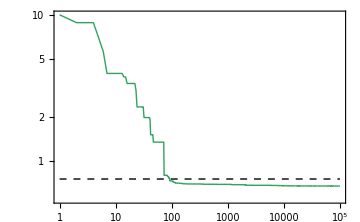

```mathematica
(* Plot of χ^2 over the generations *)
ListLogLogPlot[DataAccuracy//Abs,Joined->True,
PlotRange->{{1,10^5},All},PlotStyle->{Directive[Thick,RGBColor[0.1,0.6,0.3],Opacity[0.9]]},
Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"\\text{Generations}","\\text{Acc}(\\text{GA})"},RotateLabel->True,BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->Medium,
Epilog->{{Dashed,Thick,Line[{{1,AccGA[TEHnw[k*h,h,ωb,ωm]]},{10^5,AccGA[TEHnw[k*h,h,ωb,ωm]]}}//Log]},Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\text{Acc}(\\text{EH})"], Scaled[{0.7, 0.2}]]}]
```

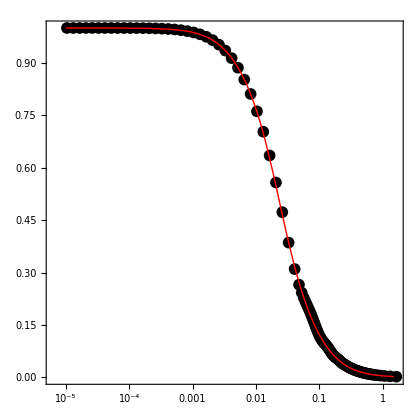

```mathematica
(* Best-Fit from the GA and the true function *)
LogLinearPlot[{Tnw[k,h,ωb,ωm]}/.h->NormPartData⟦1⟧⟦1,2⟧/.ωb->NormPartData⟦1⟧⟦1,3⟧/.ωm->NormPartData⟦1⟧⟦1,4⟧//Evaluate,{k,10^-5,1.5},PlotRange->All,PlotStyle->{Directive[Thick,Red]},
Frame->True,FrameStyle->BlackFrame,
BaseStyle->{FontFamily->"Times",FontSize->13},Axes->False,AspectRatio->0.8,
PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{GA Solution}"],
(MaTeX[#,Magnification->1.2]&)/@Style["\\text{EH}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,5}],
{0.23,0.1}]];
ListLogLinearPlot[Table[{NormPartData⟦1⟧⟦i,1⟧,NormPartData⟦1⟧⟦i,5⟧},{i,1,Length[NormPartData⟦1⟧]}],Joined->False,PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","T(k)"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotStyle->{Black,PointSize[0.02]},AspectRatio->1,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{CLASS Data}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,5}],
{0.26,0.2}]];
Show[%,%%,ImageSize->420]
```

## Evaluation

### Comparison

```mathematica
LogLinearPlot[{Tnw[k,h,ωb,ωm],TEHnw[k*h,h,ωb,ωm]}/.h->NormPartData⟦10⟧⟦1,2⟧/.ωb->NormPartData⟦10⟧⟦1,3⟧/.ωm->NormPartData⟦10⟧⟦1,4⟧//Evaluate,{k,5*10^-6,5},PlotRange->All,PlotStyle->{Directive[Thick,Red],Directive[Thick,Dashed,LightBlue],,Directive[Thick,Dashed,Green]},
Frame->True,FrameStyle->BlackFrame,
BaseStyle->{FontFamily->"Times",FontSize->13},Axes->False,AspectRatio->0.8,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\text{GA Solution}"],
(MaTeX[#,Magnification->1.4]&)/@Style["\\text{EH Formula}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,10}],
{0.3,0.25}],ImageSize->500];
ListPlot[Table[{NormPartData⟦10⟧⟦i,1⟧,NormPartData⟦10⟧⟦i,5⟧},{i,1,Length[NormPartData⟦1⟧]}],Joined->False,PlotRange->{{NormPartData⟦10⟧⟦1,1⟧,NormPartData⟦10⟧⟦-1,1⟧},All},ScalingFunctions->{"Log","Linear"},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.7]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","T(k)"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->{Black,PointSize[0.02]},AspectRatio->1,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\text{CLASS}"]}],
{0.25,0.45}],ImageSize->Medium];
Show[%,%%,ImageSize->400]
```

```mathematica
(* Fractional accuracy across scales *)
accEH=Table[{NormPartData[[i]]⟦j,1⟧,100*Abs[(1-1/(NormPartData[[i]]⟦j,5⟧)TEHnw[NormPartData[[i]]⟦j,1⟧*NormPartData[[i]]⟦j,2⟧,NormPartData[[i]]⟦j,2⟧,NormPartData[[i]]⟦j,3⟧,NormPartData[[i]]⟦j,4⟧])]},{i,1,Length[NormPartData]},{j,1,Length[NormPartData[[i]]]}];
accGAs=Table[{NormPartData[[i]]⟦j,1⟧,100*Abs[(1-1/(NormPartData[[i]]⟦j,5⟧)(Tnw[NormPartData[[i]]⟦j,1⟧,NormPartData[[i]]⟦j,2⟧,NormPartData[[i]]⟦j,3⟧,NormPartData[[i]]⟦j,4⟧]))]},{i,1,Length[NormPartData]},{j,1,Length[NormPartData[[i]]]}];
```

```mathematica
Table[Mean[accEH[[i]][[All,2]]],{i,1,Length[accEH]}]
{%//Mean,%//Min}
Table[Mean[accGAs[[i]][[All,2]]],{i,1,Length[accGAs]}]
{%//Mean,%//Min}
Position[%%,%%//Min] (* Best approximated dataset *)
```

{0.957233,0.957773,0.958162,0.958581,0.90541,0.905774,0.906255,0.90664,0.865046,0.865301,0.865517,0.865682,0.845464,0.846531,0.847723,0.848551,0.990229,0.990018,0.9902,0.99083,0.933401,0.934121,0.934586,0.935197,0.887912,0.887964,0.8882,0.888487,0.860725,0.861631,0.862591,0.863171,1.02672,1.02555,1.0252,1.02561,0.961576,0.962353,0.963184,0.964023,0.912186,0.912844,0.913566,0.914207,0.878503,0.87857,0.87882,0.879134,1.06522,1.06441,1.06388,1.06374,0.992468,0.992726,0.992757,0.993307,0.93735,0.93869,0.939689,0.940696,0.899051,0.899042,0.899277,0.899129}

{0.932944,0.845464}

{0.883365,0.884426,0.885414,0.886337,0.798922,0.799228,0.799463,0.799981,0.742209,0.741859,0.741896,0.742452,0.723127,0.722803,0.72267,0.723203,0.880095,0.878164,0.878935,0.879715,0.790626,0.789761,0.788957,0.788686,0.728042,0.72693,0.725999,0.726421,0.702578,0.702806,0.703148,0.703689,0.922004,0.920838,0.919401,0.91889,0.828876,0.829085,0.829061,0.828518,0.76347,0.764101,0.764455,0.764521,0.72755,0.728567,0.729123,0.729847,1.01657,1.0163,1.01522,1.01379,0.92485,0.92629,0.92784,0.928981,0.860829,0.861638,0.86221,0.86252,0.818485,0.819417,0.820037,0.820656}

{0.819623,0.702578}

{{29}}

```mathematica
(* Comparison of accuracy for a given set *)
ListLogLinearPlot[{accEH[[29]],accGAs[[29]]},Joined->True,PlotRange->{{NormPartData⟦29⟧⟦1,1⟧,NormPartData⟦29⟧⟦-1,1⟧},All},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{T_{i, \\text{CLASS}} - T_{i, \\text{GA}}}{T_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0.2,0.6,0.6]],Directive[Thick,RGBColor[0.9,0.1,0.4],Opacity[0.9]],Directive[Thick,RGBColor[0.9,0.5,0.4],Opacity[0.9]]},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.8]&)/@Style["\\text{EH}"],(MaTeX[#,Magnification->1.8]&)/@Style["\\text{GAs}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendFunction->"Frame",LegendMarkerSize->{35,15}],
{0.23,0.77}],Epilog->{{Dashed,Thick,Line[{{Log[10^-6],0.5},{Log[2],0.5}}]}},ImageSize->Large]
```

```mathematica
(* The accuracy of the GAs formula is in general below 0.5% when Wiggles are not relevant *)
ListLogLinearPlot[Table[accGAs[[i]],{i,1,Length[accGAs]}],Joined->True,PlotRange->{{NormPartData⟦1⟧⟦1,1⟧,NormPartData⟦1⟧⟦-1,1⟧},All},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h / \\text{Mpc}]","\\text{GAs}"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->Table[{GrayLevel[i],Thin},{i,0.2,0.8,0.6/((Length[accGAs]+1)/2)}],Epilog->{{Dashed,Thick,Line[{{Log[10^-6],0.5},{Log[2],0.5}}]}},ImageSize->420]
```

```mathematica
ListLogLinearPlot[Table[accEH[[i]],{i,1,Length[accEH]}],Joined->True,PlotRange->{{NormPartData⟦1⟧⟦1,1⟧,NormPartData⟦1⟧⟦-1,1⟧},All},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h / \\text{Mpc}]","\\text{EH}"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->Table[{GrayLevel[i],Thin},{i,0.2,0.8,0.6/((Length[accGAs]+1)/2)}],Epilog->{{Dashed,Thick,Line[{{Log[10^-6],0.5},{Log[2],0.5}}]}},ImageSize->420]
```

### Savitzky-Golay Filter

```mathematica
(* Data from CLASS (python): {k, Subscript[T, SG](k)} *)
DataFilteredTk=Import["./Data/Filtered_Tk.txt","Data"]//Quiet;
ReducedDataTnwSG=Drop[Drop[Drop[DataFilteredTk,{1,-1,2}],{1,-1,2}],{1,-1,2}]//Quiet;
Length[ReducedDataTnwSG]/2500//N (* There are 16 lists *)
PartDataTnwSG=Partition[ReducedDataTnwSG,2500];
```

64.

```mathematica
TSG=ParallelTable[Interpolation[PartDataTnwSG[[i]]],{i,1,Length[PartDataTnwSG]}];
```

```mathematica
accSG=Table[{NormPartData[[i]]⟦j,1⟧,100*Abs[(1-(TSG[[i]][NormPartData[[i]]⟦j,1⟧])/(NormPartData[[i]]⟦j,5⟧))]},{i,1,Length[NormPartData]},{j,1,Length[NormPartData[[i]]]}]//Quiet;
```

```mathematica
Table[Mean[accSG[[i]][[All,2]]],{i,1,Length[accSG]}];
{Mean[#],Min[#]}&@%
Table[Mean[accGAs[[i]][[All,2]]],{i,1,Length[accGAs]}];
{Mean[#],Min[#]}&@%
Table[Mean[accEH[[i]][[All,2]]],{i,1,Length[accEH]}];
{Mean[#],Min[#]}&@%
```

{0.793347,0.656035}

{0.819623,0.702578}

{0.932944,0.845464}

## Test

```mathematica
Quit[]
```

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
LaunchKernels[];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
```

## Data

```mathematica
Import["./Data/cosmo_params.txt","Table"][[1]]
Params=Import["./Data/cosmo_params.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As,sigma8}

```mathematica
(* 200 spectra from a Latin-Hypercube of {h, Subscript[ω, b], Subscript[ω, m], Subscript[n, s], 10^9 Subscript[A, s], Subscript[σ, 8]} *)
dir="./Data/spectra_latin_hc/";
paths=FileNameJoin[{dir,"spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

## Fitting Functions

### Eisenstein-Hu: No-Wiggles

```mathematica
Θ=Solve[2.7*x==2.728]⟦1,1,2⟧;  (* Tcmb = 2.7Θ = 2.728 -> By FIRAS *)
sh[ωb_,ωm_]:=(44.5*Log[9.83/ωm])/(√(1+10 ωb^(3/4))); (* Mpc *)
αΓ[ωb_,ωm_]:=1-0.328*Log[431*ωm]*ωb/ωm+0.38*Log[22.3*ωm]*(ωb/ωm)^2
Γeff[k_,h_,ωb_,ωm_]:=ωm/h(αΓ[ωb,ωm]+(1-αΓ[ωb,ωm])/(1+(0.43*k*sh[ωb,ωm])^4));
qeff[k_,h_,ωb_,ωm_]:=k/h*Θ^2/Γeff[k,h,ωb,ωm]; (* k in h/Mpc *)
L0eff[k_,h_,ωb_,ωm_]:=Log[2ⅇ+1.8*qeff[k,h,ωb,ωm]];
C0eff[k_,h_,ωb_,ωm_]:=14.2+731/(1+62.5*qeff[k,h,ωb,ωm]);
TEHnw[k_,h_,ωb_,ωm_]:=L0eff[k,h,ωb,ωm]/(L0eff[k,h,ωb,ωm]+C0eff[k,h,ωb,ωm]*qeff[k,h,ωb,ωm]^2)
```

### Genetic Algorithms

```mathematica
a1=101.855;
a2=21112.189;
a3=35913.065;
a4=1428.081;
b1=1.483;
b2=3.972;
b3=6.097;
b4=7.507;
q[k_,h_,ωb_,ωm_]:=(h*k)/(ωm-ωb)
Tnw[k_,h_,ωb_,ωm_]:=(1+a1*q[k,h,ωb,ωm]^b1+a2*q[k,h,ωb,ωm]^b2+ a3*q[k,h,ωb,ωm]^b3+a4*q[k,h,ωb,ωm]^b4)^(-1/4)
```

```mathematica
{LeafCount[#],Depth[#]}&/@{Tnw[k,h,ωb,ωm],TEHnw[k*h,h,ωm,ωb]}
```

{{62,9},{378,20}}

## Comparison

### Compute Normalization

```mathematica
R8=8;            (*radio en Mpc/h*)
(*Función ventana top-hat*)
WtopHat[x_]:=3/x^3(Sin[x]-x Cos[x]);
σ8=Params[[All,6]];
```

```mathematica
IntegralEH[i_]:=NIntegrate[k^(Params[[i,4]]+2) TEHnw[k*Params[[i,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2(WtopHat[R8*k])^2,{k,10^-5,100},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0EH=ParallelTable[2*π^2 σ8[[i]]^2/IntegralEH[i],{i,1,Length[Params]}];
```

```mathematica
AccEH[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-A0EH[[i]]/(PkData[[i]][[j,2]])*(PkData[[i]][[j,1]])^Params[[i,4]]*TEHnw[PkData[[i]][[j,1]]*Params[[i,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2]},{j,Length[PkData[[i]]]}];
```

```mathematica
Table[Mean[AccEH[i][[All,2]]],{i,1,Length[Params]}];
{Mean[#],Min[#],Max[#],Position[#,Min[#]][[1,1]],Position[#,Max[#]][[1,1]]}&@%
```

{1.74487,1.36167,1.95019,138,112}

```mathematica
IntegralGA[i_]:=NIntegrate[k^(Params[[i,4]]+2) Tnw[k,Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2(WtopHat[R8*k])^2,{k,0,2},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0GA=ParallelTable[2*π^2 σ8[[i]]^2/IntegralGA[i],{i,1,Length[Params]}];
```

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-A0GA[[i]]/(PkData[[i]][[j,2]])*(PkData[[i]][[j,1]])^Params[[i,4]]*Tnw[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2]},{j,Length[PkData[[i]]]}];
```

```mathematica
{Mean[#],Min[#],Max[#],Position[#,Min[#]],Position[#,Max[#]]}&@Table[Mean[AccGA[i][[All,2]]],{i,1,Length[Params]}]
WorstFit=Position[#,Max[#]][[1,1]]&@Table[Mean[AccGA[i][[All,2]]],{i,1,Length[Params]}];
BestFit=Position[#,Min[#]][[1,1]]&@Table[Mean[AccGA[i][[All,2]]],{i,1,Length[Params]}];
```

{1.1533,0.93722,1.49148,{{36}},{{193}}}

### Visual Comparison

```mathematica
i=BestFit;j=WorstFit;
ListLogLogPlot[{PkData[[i]],PkData[[j]]},Joined->True,PlotRange->{{PkData[[1]][[50,1]],PkData[[1]][[-1,1]]},{20,5*10^4}},PlotStyle->{Directive[Thickness[0.009],Dashed,Black]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","P(k) \\, [\\text{Mpc}/h]^3 "},BaseStyle->{FontFamily->"Times",FontSize->18},ImageSize->Large];
LogLogPlot[{A0GA[[i]]*k^Params[[i,4]]*Tnw[k,Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2,
A0GA[[j]]*k^Params[[j,4]]*Tnw[k,Params[[j,1]],Params[[j,2]],Params[[j,3]]]^2}//Evaluate,{k,10^-5,1.6},PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0.2,0.6,0.6]],Directive[Thick,RGBColor[0.9,0.1,0.4],Opacity[0.9]],Directive[Thick,RGBColor[0.3,0.6,0.2],Opacity[0.9]]},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.8]&)/@Style["\\text{Best~fit}"],
(MaTeX[#,Magnification->1.8]&)/@Style["\\text{Worst~fit}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendFunction->"Frame",LegendMarkerSize->{35,15}],
{0.25,0.2}]];
i=.;j=.;
Show[{%%%,%%}]
```

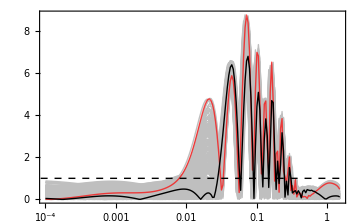

```mathematica
Module[{curves,styles,legendLabels},curves=Join[Table[AccGA[i],{i,Select[Range[Length[Params]],#!=BestFit&&#!=WorstFit&]}],{AccGA[WorstFit],AccGA[BestFit]}];
styles=Join[Table[Directive[Thin,GrayLevel[0.75]],{Length[Params]-2}],{Directive[Thick,Red,Opacity[0.7]](*Worst fit*),
Directive[Thick,Black](*Best fit*)}];
legendLabels={(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Test set}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Worst fit}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Best fit}"]};
ListLogLinearPlot[curves,Joined->True,PlotRange->{{10^-4,1.5},All},PlotStyle->styles,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"k~[h / \\text{Mpc}]","\\text{Acc}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLegends->Placed[LineLegend[styles[[-3;;]],legendLabels,LegendLayout->{"Row",3},LabelStyle->{Black,Bold,14},LegendFunction->"Frame",LegendMarkerSize->{35,15}],{0.212,0.7}],Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]}},ImageSize->Medium]//Quiet]
```

```mathematica
Module[{curves,styles,legendLabels},curves=Join[Table[AccEH[i],{i,Select[Range[Length[Params]],#!=112&&#!=138&]}],{AccEH[112],AccEH[138]}];
styles=Join[Table[Directive[Thin,GrayLevel[0.75]],{Length[Params]-2}],{Directive[Thick,Red,Opacity[0.7]](*Worst fit*),
Directive[Thick,Black](*Best fit*)}];
legendLabels={(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Test set}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Worst fit}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Best fit}"]};
ListLogLinearPlot[curves,Joined->True,PlotRange->{{10^-4,1.5},All},PlotStyle->styles,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"k~[h / \\text{Mpc}]","\\text{Acc}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLegends->Placed[LineLegend[styles[[-3;;]],legendLabels,LegendLayout->{"Row",3},LabelStyle->{Black,Bold,14},LegendFunction->"Frame",LegendMarkerSize->{35,15}],{0.212,0.7}],Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]}},ImageSize->Medium]//Quiet]
```

# Full Transfer Function

```mathematica
Quit[]
```

## Data

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[]; (* To use all the available kernels *)
Off[General::munfl];
Off[General::stop];
Off[Infinity::indet];
Off[Power::infy];
Off[Indeterminate::indet];
```

### Data

```mathematica
DataTransferFunction=Import["./Data/Transfer_Function_h_omegab_omegam.txt","Data"]//Quiet; (* Data from CLASS (python): {k, h, Subscript[ω, b], Subscript[ω, m], Φ} *)
Length[DataTransferFunction]/114//N (* There are 16 lists *)
PartData=Partition[DataTransferFunction,114]; (* Partition of data to consider each cosmology, i.e. each set {h, ωb, ωm}*)
(* Normalized data to get T(k) *)
NormPartData=Table[{#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧,(#⟦5⟧)/Max[PartData⟦i,1,5⟧]}&/@PartData⟦i⟧,{i,1,Length[PartData]}]; 
MockData=Join@@NormPartData; (* Re-Join the datasets *)
Dimensions[MockData] (* Dimensions of the dataset *)
```

64.

{7296,5}

## Fitting Functions

## Genetic Algorithms

```mathematica
a1=101.855;
a2=21112.189;
a3=35913.065;
a4=1428.081;
b1=1.483;
b2=3.972;
b3=6.097;
b4=7.507;
q[k_,h_,ωb_,ωm_]:=(h*k)/(ωm-ωb)
Tnw[k_,h_,ωb_,ωm_]:=(1+a1*q[k,h,ωb,ωm]^b1+a2*q[k,h,ωb,ωm]^b2+ a3*q[k,h,ωb,ωm]^b3+a4*q[k,h,ωb,ωm]^b4)^(-1/4)
```

## Genetic Algorithm

## Grammar, Fitness Function, and Genetic Instructions

### Grammar

```mathematica
(* Possible operations. The proposal grammar depends on each specific problem *)
poly[x_]:=x
grammar={poly}; (* Array of operations *)
```

### Genetic Code

```mathematica
(* Prior: *)
(* Subscript[T, w](k)= 1 + ((Subscript[α, b](Subscript[ω, b],Subscript[ω, m]))/(Subscript[rang, 2,1] + ((Subscript[β, b](Subscript[ω, b],Subscript[ω, m]))/ks)^Subscript[rang, 3,1])*ⅇ^(-(k/(Subscript[k, silk](Subscript[ω, b],Subscript[ω, m])))^Subscript[rang, 2,2]))*Sin[(Subscript[rang, 4,1] ks)/((Subscript[rang, 2,3] +((Subscript[β, node](Subscript[ω, m]))/ks)^Subscript[rang, 3,2])^Subscript[rang, 5,1])] *)
(* Subscript[α, b] = Subscript[rang, 5,2] + Subscript[rang, 6,1] Subscript[ω, b]^Subscript[rang, 5,3] + Subscript[rang, 5,4] Subscript[ω, m]^Subscript[rang, 2,4] *)
(* Subscript[β, b] = Subscript[rang, 7,1] + Subscript[rang, 8,1] Subscript[ω, b]^Subscript[rang, 2,5] + Subscript[rang, 9,1] Subscript[ω, m]^Subscript[rang, 2,6] *)
(* Subscript[β, node] = Subscript[rang, 10,1] Subscript[ω, m]^Subscript[rang, 5,5] *)
length=10; depth=10; (* Number of nucleotides and genes. Chromosomes will be 10x10 matrices *)
(* Ranges to compute random numbers specifying the expression of an individual *)
rang1={1,Length[grammar]}; (* To choose an operation in the grammar *)
rang2={0.5,1.5}; (* Look at the prior formula *)
rang3={0.5,3.5};
rang4={0.5,0.8};
rang5={0,1};
rang6={-0.5,0}; 
rang7={1,2}; 
rang8={-50,0};
rang9={0,60};
rang10={0.1,2};
```

### Fitness Function

```mathematica
(* Accuracy of an Individual -> Acc% = 100|Subscript[f, GA] - Subscript[f, num]|/Subscript[f, num] *)
AccGA[f_]:=AccGA[f]=Module[{temp,ft},
ft=(f/.{x->#1,y->#2,z->#3,w->#4})&; (* Individual *)
temp=Mean[Table[1/MockData⟦i,5⟧Abs[MockData⟦i,5⟧-ft[MockData⟦i,1⟧,MockData⟦i,2⟧,MockData⟦i,3⟧,MockData⟦i,4⟧]]*100,{i,1,Length[MockData]}]]; (* Accuracy measure *)
If[MatchQ[temp,_Real]&&$MinNumber<temp<$MaxNumber,temp,1. 10^230]] (* Space-Time constraints in the computation *)
```

## Genetic Operators

### Mutation

```mathematica
mutation[kid_]:=Module[{mut,rep},
rep={RandomInteger[{0,length}],RandomInteger[{0,depth}]}; (* To decide where apply a mutation *)
mut=Which[
rep⟦2⟧==1,RandomInteger[rang1], (* If rep⟦2⟧ == 1 -> modify the operation *)
rep⟦2⟧==2,RandomReal[rang2],
rep⟦2⟧==3,RandomReal[rang3], 
rep⟦2⟧==4,RandomReal[rang4],
rep⟦2⟧==5,RandomReal[rang5],
rep⟦2⟧==6,RandomReal[rang6],
rep⟦2⟧==7,RandomReal[rang7],
rep⟦2⟧==8,RandomReal[rang8], 
rep⟦2⟧==9,RandomReal[rang9], 
rep⟦2⟧==10,RandomReal[rang10]];
ReplacePart[kid,rep->mut]] (* Replace rep = {a, b} by mut = c in kid *)
```

### Crossover

```mathematica
cross[{kid1_,kid2_}]:=Module[{len},
len=RandomInteger[{1,length-1}]; (* Till length - 1 to not exceed the length of the chromosomes *)
{Join[kid1⟦1;;len⟧,kid2⟦(len+1);;-1⟧], (* Interchange of nucleotides *)
Join[kid1⟦(len+1);;-1⟧,kid2⟦1;;len⟧]}]
```

## Selection Scheme

### Tournament Selection

```mathematica
toursize=4; (* Participants in the tournament *)
tournament[fit_,tours_]:=Sort[RandomSample[fit,tours], (* Take "tours" members from "fitnesses-set" at random *)
#1⟦1⟧>#2⟦1⟧&]⟦1,2⟧ (* Organize from greatest to smallest and take the individual with the best fit *)
negativetournament[fit_,tours_]:=Sort[RandomSample[fit,tours], 
#1⟦1⟧>#2⟦1⟧&]⟦-1,2⟧ (* The same but taking the individual with the worst fit *)
```

## Genetic Algorithm

### Evolution of the Genetic Algorithm

```mathematica
(* Sound horizon expression from GAs [arXiv:2106.00428] *)
c1=0.00785436;c2=0.177084;c3=0.00912388;c4=0.618711;
c5=11.9611;c6=2.81343;c7=0.784719;
sGA[ωb_,ωm_]:=1/(c1*ωb^c2+c3*ωm^c4+c5*ωb^c6*ωm^c7)
(* Diffusion scale from minimization process using CLASS data: Subscript[k, s] = 0.373 y^0.419+0.195 z^1.095 *)
kSilk[z_,w_]:=0.373 z^0.419+0.195 w^1.0957
selectionrate=0.3; (* Portion of the population to be sorted and replaced *)
(* Subscript[α, b] = Subscript[a, 1] + Subscript[a, 2] Subscript[ω, b]^Subscript[a, 3] + Subscript[a, 4] Subscript[ω, m]^Subscript[a, 5] *)
αbGA[y_,z_,kid_,gram_]:=Sum[ gram⟦kid⟦i,1⟧⟧@(kid⟦i+1,5⟧+kid⟦i,6⟧y^kid⟦i+2,5⟧+kid[[i+3,5]] z^kid⟦i+3,2⟧),{i,1,1}]
(* Subscript[β, b] = Subscript[a, 1] + Subscript[a, 2] Subscript[ω, b]^Subscript[a, 3] + Subscript[a, 4] Subscript[ω, m]^Subscript[a, 5] *)
βbGA[y_,z_,kid_,gram_]:=Sum[ gram⟦kid⟦i,1⟧⟧@(kid⟦i,7⟧+kid⟦i,8⟧y^kid⟦i+4,2⟧+kid[[i,9]] z^kid⟦i+5,2⟧),{i,1,1}]
(* Subscript[β, node] = Subscript[a, 1] Subscript[ω, m]^Subscript[a, 2] *)
βnodeGA[z_,kid_,gram_]:=Sum[ gram⟦kid⟦i,1⟧⟧@(kid⟦i,10⟧z^kid⟦i+4,5⟧),{i,1,1}]
(* Creator -> converts the chromosomes in "individuals": Subscript[T, nw](1+Subscript[α, b]/(Subscript[a, 1]+(Subscript[β, b]/ks)^Subscript[a, 2])ⅇ^(-(k/Subscript[k, Silk])^Subscript[a, 3]))Sin((Subscript[a, 4] ks + Subscript[a, 8] Subscript[ω, m]^a9)/((Subscript[a, 5]+(Subscript[β, node]/ks)^Subscript[a, 6])^Subscript[a, 7])) *)
funcGAs[x_,y_,z_,w_,kid_,gram_]:=Tnw[x,y,z,w](1+(αbGA[z,w,kid,gram]/(kid[[1,2]]+(βbGA[z,w,kid,gram]/(x*y*sGA[z,w]))^kid[[1,3]])*ⅇ^(-((x*y)/(kid[[7,2]]*kSilk[z,w]))^kid[[2,2]]))*Sin[(kid[[1,4]]*(x*y*sGA[z,w]+kid[[2,4]]*w^kid[[2,6]]))/((kid[[3,2]]+(βnodeGA[w,kid,gram]/(x*y*sGA[z,w]))^kid[[2,3]])^kid[[1,5]])]);
GAevo[randomseed_,maxgens_,pop_,crossrate_,mutrate_,verbose_]:=Module[{prog,bestfitperstep,chromosomes,t1,pigs,fitness,p1,p2,maxchilds},
maxchilds=Round[selectionrate*pop,2]; (* Around 1/3 of the population will be selected as the best *)
SeedRandom[randomseed];
ParallelEvaluate[SeedRandom[randomseed]];
bestfitperstep={}; (* store: {fitness, individual, chromosome} *)
(* Progenitors -> Creation of "pop" chromosomes: 8 nucleotides for each gene and a total of 8 genes *)
chromosomes=Table[{RandomInteger[rang1],RandomReal[rang2],RandomReal[rang3],RandomReal[rang4],RandomReal[rang5],RandomReal[rang6],RandomReal[rang7],RandomReal[rang8],RandomReal[rang9],RandomReal[rang10]},{pop},{length}];
t1=AbsoluteTime[];
(* "pigs" is a "prior". It is computed for all pop. Its form depends on the problem *)
Do[
pigs=funcGAs[x,y,z,w,#,grammar]&/@chromosomes;
(* {-χ^2 for jth pig , counter j} sorted from the greatest to the smallest fitness *)
fitness=Sort[ParallelTable[{-MemoryConstrained[TimeConstrained[AccGA[pigs⟦j⟧],2,10^230],10^8,10^230],j},{j,1,Length[pigs]}],#1⟦1⟧>#2⟦1⟧&];
(* Append to bestfitperstep the greatest fitness, and its corresponding expression, and chromosomes *)
AppendTo[bestfitperstep,{fitness⟦1,1⟧,pigs⟦fitness⟦1,2⟧⟧,chromosomes⟦fitness⟦1,2⟧⟧}];
(* Selection of the best parents -> They are divided in pairs *)
p1=Partition[RandomSample[Table[negativetournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];p2=Partition[RandomSample[Table[tournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];
(* Crossover of pairs *)
Do[{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}=If[RandomReal[{0,1}]<crossrate,
cross[{chromosomes⟦p2⟦jj,1⟧⟧,chromosomes⟦p2⟦jj,2⟧⟧}], (* Worst are replaced by the children of the fittest *)
{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}];, (* The worst are replaced by the fittest *)
{jj,1,Length[p1]}];
(* Mutation *)
Do[{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}=If[RandomReal[{0,1}]<mutrate,
{mutation[chromosomes⟦p2⟦jj,1⟧⟧],mutation[chromosomes⟦p2⟦jj,2⟧⟧]}, (* Worst are replaced by fittest mutations *)
{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}];, (* The worst are replaced by the fittest *)
{jj,1,Length[p1]}];
Off[General::munfl];
Off[General::stop];
prog`int++,{maxgens}];
Off[General::munfl];
Off[General::stop];
If[verbose==True,
Print["Time taken: ",Round[AbsoluteTime[]-t1]," secs or ",Round[(AbsoluteTime[]-t1)/60], " mins"];
Print["Accuracy = ",Abs[fitness⟦1,1⟧]];
Print["Best-fit function is: "];
Print[bestfitperstep⟦-1,2⟧];
Speak["Listo el pollo"];];
bestfitperstep]
```

## Evolution

### Several Random Seeds

```mathematica
(* We try with several random seeds *)
generations=100;
SaveState={};
samples=100;
prog`int=0;prog`pop=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
ProgressIndicator[Dynamic[prog`pop],{0,samples}]
t0=AbsoluteTime[];
Do[GApop1[j]=GAevo[1234j,generations,100,0.7,0.35,False]//Quiet;
Print["Time: ", AbsoluteTime[]-t0];
AppendTo[SaveState,{GApop1[j]⟦-1,1⟧,1234j}]; (* Save the accuracy and random seed *)
Export["Save_State_BAO.txt",SaveState,"Table"];
prog`pop++;prog`int=0;,{j,1,samples}];
```

Time: 70.860143

Time: 174.99867

Time: 292.63607

Time: 370.142873

Time: 446.988515

Time: 520.761201

Time: 623.371711

Time: 725.627428

Time: 803.531605

Time: 879.752822

Time: 957.098678

Time: 1070.42471

Time: 1163.17224

Time: 1238.67247

Time: 1316.68112

Time: 1396.46071

Time: 1497.218

Time: 1597.61478

Time: 1678.666

Time: 1758.3013

Time: 1838.55211

Time: 1941.79325

Time: 2050.37475

Time: 2133.902

Time: 2214.30965

Time: 2292.68465

Time: 2374.66533

Time: 2452.56325

Time: 2532.62575

Time: 2614.35826

Time: 2696.27703

Time: 2787.78428

Time: 2897.09365

Time: 2973.89494

Time: 3055.57674

Time: 3132.398

Time: 3248.73176

Time: 3338.21206

Time: 3417.81991

Time: 3495.09351

Time: 3572.65561

Time: 3653.294695

Time: 3734.141151

Time: 3817.221803

Time: 3895.013779

Time: 3973.774389

Time: 4043.439765

Time: 4133.647003

Time: 4214.425255

Time: 4292.379776

Time: 4380.076401

Time: 4480.405785

Time: 4556.933954

Time: 4634.637636

Time: 4717.254935

Time: 4792.160169

Time: 4913.917292

Time: 5000.041912

Time: 5078.739993

Time: 5160.067477

Time: 5236.550933

Time: 5317.654493

Time: 5394.869839

Time: 5473.816753

Time: 5549.033137

Time: 5621.029038

Time: 5697.213197

```mathematica
(* Plot the accuracy of GA solutions *)
Severalχ2=ListLogLogPlot[Table[GApop1[jj]⟦All,1⟧//Abs,{jj,1,67}],Joined->True,PlotRange->{{1,generations},All},Frame->True,PlotStyle->{Directive[Gray,Thickness[0.001]]},FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"\\text{Generations}","\\chi^2"},BaseStyle->{FontFamily->"Times",FontSize->13},RotateLabel->False,ImageSize->380,
Epilog->{{Dashed,Thick,Red,Line[{{1,0.67},{generations,0.67}}//Log]},{Dashed,Thick,Red,Line[{{1.2,0.33},{2.5,0.33}}//Log]},Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\text{No Wiggles}"], Scaled[{0.35, 0.15}]]}]
```

```mathematica
DataSaved=Import["Save_State_BAO.txt","Data"];
```

```mathematica
(* Best individual *)
Elite=Max[DataSaved⟦All,1⟧];
PosElite=Position[DataSaved,Elite];
DataSaved⟦PosElite⟦1,1⟧⟧ (* Determine the random seed and the accuracy of the winner *)
```

{-0.296972,64168}

### Long Run For the Winner

```mathematica
generations=100000;
prog`int=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
(* {randomseed, max generations, population, crossover-rate, mutation-rate, verbose (True/False)} *)
GApop=GAevo[64168,generations,100,0.7,0.35,True]//Quiet;(* Retrieve bestfitperstep = {fitness, expression, chromosomes} *)
```

Time taken: 65775 secs or 1096 mins

Accuracy = 0.291587

Best-fit function is:

(1+(ⅇ^(-1.36418 ((x y)/(0.195 w^1.0957+0.373 z^0.419))^0.991405) (0.10047+0.000523634 w^1.49988-0.148511 z^0.763241) Sin[(0.789909 (0.542643/w^0.26955+(x y)/(0.00912388 w^0.618711+0.00785436 z^0.177084+11.9611 w^0.784719 z^2.81343)))/((0.734902+1.00587 ((w^0.234948 (0.00912388 w^0.618711+0.00785436 z^0.177084+11.9611 w^0.784719 z^2.81343))/(x y))^1.19807)^0.739669)])/(1.03922+(1/(x y)(1.47345+46.0264 w^1.24458-49.9998 z^0.961643) (0.00912388 w^0.618711+0.00785436 z^0.177084+11.9611 w^0.784719 z^2.81343))^2.73452))/(1+101.855 ((x y)/(w-z))^1.483+21112.2 ((x y)/(w-z))^3.972+35913.1 ((x y)/(w-z))^6.097+1428.08 ((x y)/(w-z))^7.507)^(1/4)

```mathematica
(* Check the correct limits of the GA solution *)
GApop⟦-1,2⟧/.x->0//Quiet
Limit[GApop⟦-1,2⟧/.y->0.7/.z->0.022/.w->0.13,x->∞]
```

1.

0.

```mathematica
TGAs[x_,y_,z_,w_]:=("1"+(ⅇ^("-1.364" ((x y)/("0.195" w^("1.096")+"0.373" z^("0.419")))^("0.991")) ("0.100"+"0.001" w^("1.500")-"0.149" z^("0.763")) Sin[("0.790" (("0.543")/w^("0.270")+(x y)/("0.009" w^("0.619")+"0.008" z^("0.177")+"11.961" w^("0.785") z^("2.813"))))/(("0.735"+"1.006" (("0.009" w^("0.854")+"0.008" w^("0.235") z^("0.177")+"11.961" w^("1.020") z^("2.813"))/(x y))^("1.198"))^("0.740"))])/("1.039"+((("1.473"+"46.026" w^("1.245")-"50.000" z^("0.962")) ("0.009" w^("0.619")+"0.008" z^("0.177")+"11.961" w^("0.785") z^("2.813")))/(x y))^("2.735")))/("1"+"101.855" ((x y)/(w-z))^("1.483")+"21112.189" ((x y)/(w-z))^("3.972")+"35913.065" ((x y)/(w-z))^("6.097")+"1428.081" ((x y)/(w-z))^("7.507"))^("1"/"4")
```

```mathematica
Export["Generations_Accuracy_BAO.txt",Abs[GApop⟦All,1⟧],"Table"];
```

### Silk Correction

#### Accuracy

```mathematica
accGAs=Table[{NormPartData[[i]]⟦j,1⟧,100*Abs[1-1/(NormPartData[[i]]⟦j,5⟧)(TGAs[NormPartData[[i]]⟦j,1⟧,NormPartData[[i]]⟦j,2⟧,NormPartData[[i]]⟦j,3⟧,NormPartData[[i]]⟦j,4⟧])]},{i,1,Length[NormPartData]},{j,1,Length[NormPartData[[i]]]}];
```

```mathematica
{Mean[#],Min[#],Max[#]}&@Table[Mean[accGAs[[i]][[All,2]]],{i,1,Length[accGAs]}]
```

{0.291587,0.220021,0.399866}

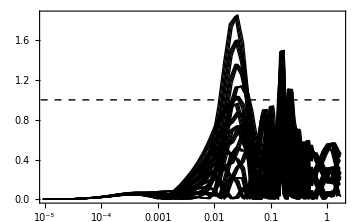

```mathematica
(* The accuracy of the GAs formula is in general below 1% for all scales *)
ListLogLinearPlot[Table[accGAs[[i]],{i,1,Length[accGAs]}],Joined->True,PlotRange->{{NormPartData⟦1⟧⟦1,1⟧,NormPartData⟦1⟧⟦-1,1⟧},All},PlotStyle->{Directive[Thin,Black]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"k \\, [h / \\text{Mpc}]","\\text{Acc}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->{Opacity[0.5]},Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]}},ImageSize->Medium]
(* There is a problematic peak around k = 0.01 h/Mpc *)
```

```mathematica
accGAs=Table[{NormPartData[[i]]⟦j,1⟧,100*(1-1/(NormPartData[[i]]⟦j,5⟧)(TGAs[NormPartData[[i]]⟦j,1⟧,NormPartData[[i]]⟦j,2⟧,NormPartData[[i]]⟦j,3⟧,NormPartData[[i]]⟦j,4⟧]))},{i,1,Length[NormPartData]},{j,1,Length[NormPartData[[i]]]}];
```

```mathematica
Table[Mean[accGAs[[i]][[All,2]]],{i,1,Length[accGAs]}]
{%//Mean,%//Min}
```

{0.262993,0.262342,0.261786,0.26122,0.155617,0.154781,0.15429,0.15384,0.0694546,0.0689027,0.0682801,0.0676693,0.000268219,-0.000375576,-0.000910648,-0.00158285,0.156227,0.155469,0.154979,0.154299,0.0443904,0.0435042,0.0427797,0.0422255,-0.0452638,-0.0460333,-0.0466527,-0.0473533,-0.117093,-0.117874,-0.11852,-0.119231,0.0509578,0.049903,0.0493259,0.0487969,-0.0657983,-0.0667583,-0.0675711,-0.0680716,-0.159162,-0.159942,-0.160622,-0.161455,-0.233607,-0.234538,-0.235135,-0.236113,-0.0531461,-0.0543512,-0.05497,-0.0557184,-0.174793,-0.175911,-0.17678,-0.177665,-0.271996,-0.272851,-0.273752,-0.274497,-0.349484,-0.350292,-0.351129,-0.351936}

{-0.0467912,-0.351936}

```mathematica
(* The accuracy of the GAs formula is in general below 1% for all scales *)
ListLogLinearPlot[Table[accGAs[[i]],{i,1,Length[accGAs]}],Joined->True,PlotRange->{{NormPartData⟦1⟧⟦1,1⟧,NormPartData⟦1⟧⟦-1,1⟧},All},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h / \\text{Mpc}]","\\text{GAs}"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->{Opacity[0.5]},Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1.5},{Log[2],1.5}}],Line[{{Log[10^-6],1},{Log[2],1}}],Line[{{Log[10^-6],-1},{Log[2],-1}}]}},ImageSize->600]
(* There are excess and defects around k = 0.01 h/Mpc *)
```

```mathematica
(* We add a correction for the amplitude supression due to photon difussion *)
TGAsMin[x_,y_,z_,w_,A_,σ_,ks_]:=TGAs[x,y,z,w](1+A*ⅇ^(-((x-ks)/σ)^2))
χ2WinnerMin[A_,σ_,ks_]:=Mean[ParallelTable[1/MockData⟦i,5⟧Abs[MockData⟦i,5⟧-TGAsMin[MockData⟦i,1⟧,MockData⟦i,2⟧,MockData⟦i,3⟧,MockData⟦i,4⟧,A,σ,ks]]*100,{i,1,Length[MockData]}]];
FindMinimum[χ2WinnerMin[A,σ,ks],{{A,-0.06},{σ,0.06},{ks,0.19}},MaxIterations->1000,AccuracyGoal->10,PrecisionGoal->10]//Quiet
BestFit=%[[2]];
```

{0.250269,{A→-0.00624985,σ→0.0626959,ks→0.199421}}

## Evaluation

```mathematica
DataGenerations=Import["Generations_Accuracy_BAO.txt","Data"]//Flatten;
```

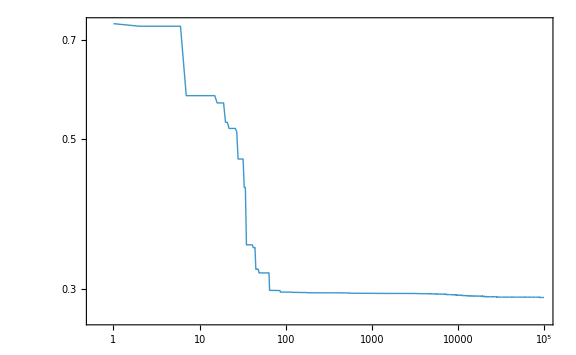

```mathematica
(* Plot of χ^2 over the generations -> We should modify the configuration of the GA *)
ListLogLogPlot[GApop[[All,1]]//Abs,Joined->True,
PlotRange->All,PlotStyle->Thick,
Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\text{Generations}","\\%\\mathrm{Acc}"},RotateLabel->True,BaseStyle->{FontFamily->"Times",FontSize->18},ImageSize->Large]
```

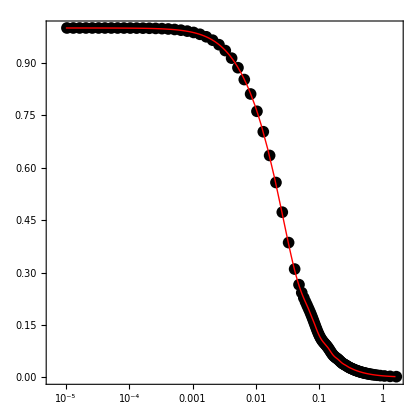

```mathematica
(* Best-Fit from the GA and the true function *)
LogLinearPlot[{TGAsMin[x,y,z,w,A,σ,ks]/.BestFit}/.y->NormPartData⟦1⟧⟦1,2⟧/.z->NormPartData⟦1⟧⟦1,3⟧/.w->NormPartData⟦1⟧⟦1,4⟧//Evaluate,{x,10^-5,1.6},PlotRange->All,PlotStyle->{Directive[Thick,Red]},
Frame->True,FrameStyle->BlackFrame,
BaseStyle->{FontFamily->"Times",FontSize->13},Axes->False,AspectRatio->0.8,
PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{GA Solution}"],
(MaTeX[#,Magnification->1.2]&)/@Style["\\text{EH}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,5}],
{0.23,0.1}]];
ListLogLinearPlot[Table[{NormPartData⟦1⟧⟦i,1⟧,NormPartData⟦1⟧⟦i,5⟧},{i,1,Length[NormPartData⟦1⟧]}],Joined->False,PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"k \\, [h / \\text{Mpc}]","T(k)"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotStyle->{Black,PointSize[0.02]},AspectRatio->1,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{CLASS Data}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,5}],
{0.26,0.2}]];
Show[%,%%,ImageSize->420]
```

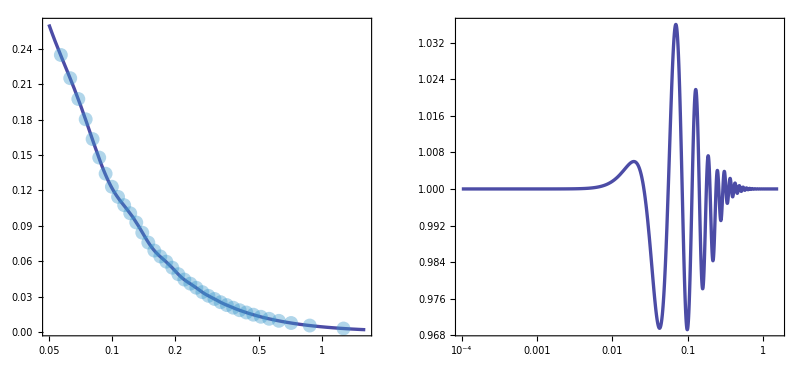

```mathematica
ListLogLinearPlot[Drop[Table[{NormPartData[[11]][[i,1]],NormPartData[[11]][[i,5]]},{i,40,114}],{1,-1,2}],PlotStyle->{Directive[PointSize[0.025],Opacity[0.4]]},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.6]&)/@Style["\\texttt{CLASS}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,15},LegendMarkerSize->15],
{0.19,0.2}]];
LogLinearPlot[TGAsMin[x,y,z,w,A,σ,ks]/.BestFit/.y->NormPartData[[11]][[1,2]]/.z->NormPartData[[11]][[1,3]]/.w->NormPartData[[11]][[1,4]]//Evaluate,{x,5*10^-2,1.6},PlotRange->All,PlotStyle->{Directive[Thickness[0.006],RGBColor[0,0,0.5],Opacity[0.7]]},
Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"k \\, [h/\\text{Mpc}]"},
BaseStyle->{FontFamily->"Times",FontSize->18},Axes->False,AspectRatio->0.8,
PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.6]&)/@Style["\\text{GA Solution}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,10},LegendMarkerSize->{25,15}],
{0.25,0.1}]];
Show[{%,%%}];
LogLinearPlot[(TGAsMin[x,y,z,w,A,σ,ks]/TGAnw[x,y,z,w])/.BestFit/.y->NormPartData[[11]][[1,2]]/.z->NormPartData[[11]][[1,3]]/.w->NormPartData[[11]][[1,4]]//Evaluate,{x,10^-4,1.6},PlotRange->All,PlotStyle->{Directive[Thickness[0.006],RGBColor[0,0,0.5],Opacity[0.7]]},
Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"k \\, [h/\\text{Mpc}]"},
BaseStyle->{FontFamily->"Times",FontSize->18},Axes->False,AspectRatio->0.8,
PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.6]&)/@Style["\\text{GA Solution}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,15},LegendMarkerSize->{25,15}],
{0.3,0.1}]];
GraphicsRow[{%%,%},Frame->All,ImageSize->Full]
(* Left: Zoom of the fit where BAOs are found. Right: BAOs signal. *)
```

#### Accuracy

```mathematica
accGAs=Table[{NormPartData[[i]]⟦j,1⟧,100*Abs[(1-1/(NormPartData[[i]]⟦j,5⟧)(TGAsMin[NormPartData[[i]]⟦j,1⟧,NormPartData[[i]]⟦j,2⟧,NormPartData[[i]]⟦j,3⟧,NormPartData[[i]]⟦j,4⟧,A,σ,ks])/.BestFit)]},{i,1,Length[NormPartData]},{j,1,Length[NormPartData[[i]]]}];
```

```mathematica
Table[Mean[accGAs[[i]][[All,2]]],{i,1,Length[accGAs]}]
{%//Mean,%//Min}
```

{0.374882,0.379245,0.383242,0.387905,0.287309,0.292014,0.297428,0.302422,0.253689,0.260304,0.266015,0.271237,0.269573,0.272595,0.27791,0.283334,0.290376,0.290844,0.295349,0.300619,0.198281,0.198077,0.200632,0.204777,0.169594,0.162481,0.161978,0.16512,0.206885,0.199536,0.194212,0.192252,0.273083,0.271248,0.271555,0.272356,0.191452,0.184745,0.181503,0.180193,0.160511,0.155417,0.15039,0.145108,0.21474,0.210041,0.205778,0.20336,0.349411,0.346369,0.345036,0.344508,0.27063,0.267571,0.264694,0.262683,0.221184,0.218941,0.217091,0.216194,0.286158,0.283168,0.281533,0.280455}

{0.250269,0.145108}

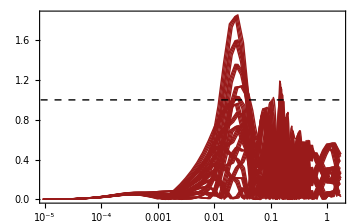

```mathematica
(* The accuracy of the GAs formula is in general below 1% for all scales *)
ListLogLinearPlot[Table[accGAs[[i]],{i,1,Length[accGAs]}],Joined->True,PlotRange->{{NormPartData⟦1⟧⟦1,1⟧,NormPartData⟦1⟧⟦-1,1⟧},All},PlotStyle->{Directive[Thin,RGBColor[0.6,0.1,0.1]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"k \\, [h / \\text{Mpc}]","\\text{Acc}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->{Opacity[0.5]},Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]}},ImageSize->Medium]
(* There is a problematic peak around k = 0.01 h/Mpc *)
```

```mathematica
accGAs=Table[{NormPartData[[i]]⟦j,1⟧,100*(1-1/(NormPartData[[i]]⟦j,5⟧)(TGAsMin[NormPartData[[i]]⟦j,1⟧,NormPartData[[i]]⟦j,2⟧,NormPartData[[i]]⟦j,3⟧,NormPartData[[i]]⟦j,4⟧,A,σ,ks]/.BestFit))},{i,1,Length[NormPartData]},{j,1,Length[NormPartData[[i]]]}];
```

```mathematica
Table[Mean[accGAs[[i]][[All,2]]],{i,1,Length[accGAs]}]
{%//Mean,%//Min}
```

{0.360647,0.360117,0.359629,0.359085,0.253323,0.252626,0.252217,0.251802,0.16718,0.166783,0.166258,0.165696,0.097986,0.0975133,0.0970904,0.0964805,0.25406,0.253427,0.253009,0.252354,0.142279,0.141535,0.140897,0.140382,0.0526461,0.0520359,0.0515178,0.0508698,-0.0191888,-0.0197944,-0.0203239,-0.0209698,0.148967,0.148042,0.147541,0.14704,0.0322706,0.0314575,0.0307352,0.0302769,-0.0610688,-0.0616849,-0.0622599,-0.0630365,-0.135519,-0.136269,-0.136746,-0.137654,0.0450382,0.0439677,0.0434281,0.0427118,-0.0765452,-0.077512,-0.078286,-0.0791253,-0.173721,-0.174408,-0.1752,-0.175885,-0.251212,-0.251835,-0.252548,-0.253282}

{0.051357,-0.253282}

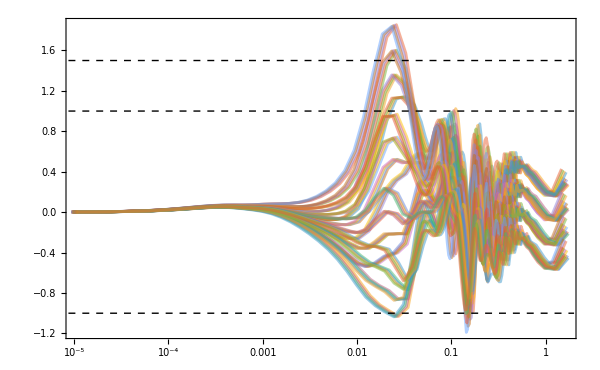

```mathematica
(* The accuracy of the GAs formula is in general below 1% for all scales *)
ListLogLinearPlot[Table[accGAs[[i]],{i,1,Length[accGAs]}],Joined->True,PlotRange->{{NormPartData⟦1⟧⟦1,1⟧,NormPartData⟦1⟧⟦-1,1⟧},All},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h / \\text{Mpc}]","\\text{GAs}"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->{Opacity[0.5]},Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1.5},{Log[2],1.5}}],Line[{{Log[10^-6],1},{Log[2],1}}],Line[{{Log[10^-6],-1},{Log[2],-1}}]}},ImageSize->600]
(* There are excess and defects around k = 0.01 h/Mpc *)
```

## Test

```mathematica
Quit[]
```

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
LaunchKernels[];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
```

## Data

```mathematica
Import["./Data/cosmo_params.txt","Table"][[1]]
Params=Import["./Data/cosmo_params.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As,sigma8}

```mathematica
(* 200 spectra from latin-hypercube {h, Subscript[ω, b], Subscript[ω, m], Subscript[n, s], 10^9 Subscript[A, s]} *)
dir="./Data/spectra_latin_hc/";
paths=FileNameJoin[{dir,"spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

## Fitting Function

### Eisenstein-Hu: No-Wiggles

```mathematica
Θ=Solve[2.7*x==2.728]⟦1,1,2⟧;  (* Tcmb = 2.7Θ = 2.728 -> By FIRAS *)
sEH[ωb_,ωm_]:=(44.5*Log[9.83/ωm])/(√(1+10 ωb^(3/4))); (* Mpc *)
αΓ[ωb_,ωm_]:=1-0.328*Log[431*ωm]*ωb/ωm+0.38*Log[22.3*ωm]*(ωb/ωm)^2
Γeff[k_,h_,ωb_,ωm_]:=ωm/h(αΓ[ωb,ωm]+(1-αΓ[ωb,ωm])/(1+(0.43*k*sEH[ωb,ωm])^4));
qeff[k_,h_,ωb_,ωm_]:=k/h*Θ^2/Γeff[k,h,ωb,ωm]; (* k in h/Mpc *)
L0eff[k_,h_,ωb_,ωm_]:=Log[2ⅇ+1.8*qeff[k,h,ωb,ωm]];
C0eff[k_,h_,ωb_,ωm_]:=14.2+731/(1+62.5*qeff[k,h,ωb,ωm]);
TEHnw[k_,h_,ωb_,ωm_]:=L0eff[k,h,ωb,ωm]/(L0eff[k,h,ωb,ωm]+C0eff[k,h,ωb,ωm]*qeff[k,h,ωb,ωm]^2)
```

### Eisenstein-Hu

```mathematica
(* All the formulas are extracted from EH97I[9709112 v1] paper,unless stated. *)
Θ=Solve[2.7*x==2.728]⟦1,1,2⟧;  (* Tcmb = 2.7Θ = 2.728 -> By FIRAS *)
(* See Eq. (11) *)
a1EH[ωm_]:=(46.9ωm)^0.670 (1+(32.1 ωm)^-0.532)
a2EH[ωm_]:=(12.0 ωm)^0.424 (1+(45.0 ωm)^-0.582) 
αc[ωb_,ωm_]:=a1EH[ωm]^(-ωb/ωm)*a2EH[ωm]^(-(ωb/ωm)^3)
(* See Eq. (12) *)
b1EH[ωm_] := 0.944 (1+(458 ωm)^-0.708)^-1 
b2EH[ωm_]:=(0.395 ωm)^-0.0266 
βc[ωb_,ωm_]:=(1+b1EH[ωm](((ωm - ωb)/ωm)^b2EH[ωm]-1))^-1 
(* Redshift at drag epoch -> See Eq. (4) *)
b1d[ωm_]:=0.313 ωm^-0.419 (1 + 0.607 ωm^0.674) 
b2d[ωm_]:=0.238 ωm^0.223 
zd[ωb_,ωm_]:=1291*ωm^0.251/(1 + 0.659 ωm^0.828)(1 + b1d[ωm] ωb^b2d[ωm]) 
zeqEH[ωm_]:=2.5*10^4 ωm*Θ^-4 (* Redshift at equilibrium epoch -> See Eq. (2) *)
keqEH[ωm_]:=7.46*10^-2 ωm*Θ^-2  (* scale at equilibrium epoch -> See Eq. (3) *)
qEH[k_,ωm_] := k/(13.41 keqEH[ωm])  (* See Eq. (10) *)
REH[z_,ωb_]:=31.5*ωb*Θ^-4*(z/10^3)^-1  (* Baryon-Photon ratio -> See Eq. (5) *)
yEH[z_,ωm_]:=(1+zeqEH[ωm])/(1+z) (* Useful variable for calculations in LS limit -> See Eq.(8.20) in Dodelson 2 *)
(* Sub-horizon solution of the Mezsaros' eq. -> See Eq. (8.63) in Dodelson 2 *)
GEH[z_,ωm_]:=yEH[z, ωm] (-6 √(1+yEH[z,ωm])+(2+3yEH[z,ωm])Log[(√(1 + yEH[z, ωm])+1)/(√(1 + yEH[z, ωm])-1)]) 
(* Silk damping scale -> See Eq. (7) *)
kSilkEH[ωb_,ωm_]:=1.6 ωb^0.52*ωm^0.73(1+(10.4 ωm)^-0.95) (* [(Mpc^-1)]*)
βnode[ωm_]:=8.41*ωm^0.435 (* Shifting of nodes parameter -> See Eq. (23) *)
st[k_,ωb_,ωm_]:=sEH[ωb,ωm]/((1+(βnode[ωm]/(k*sEH[ωb, ωm]))^3)^(1/3)) (* Shifting of oscillations nodes -> See Eq. (22) *)
(* Amplitude of small scale contributions -> See Eq. (14) *)
αb[ωb_,ωm_]:=2.07*keqEH[ωm]*sEH[ωb,ωm] (1+REH[zd[ωb,ωm],ωb])^(-3/4)GEH[yEH[zd[ωb,ωm],ωm], ωm] 

(* Small scale contributions -> See Eq. (24) *)
βb[ωb_,ωm_]:=0.5+ωb/ωm+(3-2 ωb/ωm) √((17.2 ωm)^2+1)
fEH[k_,ωb_,ωm_]:=1/(1 + ((k*sEH[ωb, ωm])/5.4)^4) (* See Eq (18) *)
Cf[k_,ωb_,ωm_]:=14.2/αc[ωb,ωm]+386/(1 + 69.9*qEH[k,ωm]^1.08) (* See Eq. (20) *)
Cfαc1[k_,ωb_,ωm_]:=14.2 + 386/(1 + 69.9*qEH[k,ωm]^1.08) (* Cf with αc = 1*)
(* See Eq. (19) *)
T0[k_,ωb_,ωm_]:=Log[ⅇ + 1.8*βc[ωb,ωm]*qEH[k,ωm]]/(Log[ⅇ+1.8 βc[ωb,ωm]*qEH[k,ωm]]+Cf[k,ωb,ωm]*qEH[k,ωm]^2)
(* See Eqs. (19) and (20) in EH97: T0(k, 1, βc) means αc = 1 in Eq. (20) *)
T01[k_,ωb_,ωm_]:=Log[ⅇ+1.8*βc[ωb,ωm]*qEH[k,ωm]]/(Log[ⅇ + 1.8 βc[ωb,ωm]*qEH[k,ωm]]+Cfαc1[k,ωb,ωm]*qEH[k,ωm]^2)
(* See Eq. (19) in EH97: T0(k, 1, 1) means αc = 1 in Eq. (20) and βc = 1 in Eq. (19) *)
T011[k_,ωb_,ωm_]:=Log[ⅇ+1.8*qEH[k,ωm]]/(Log[ⅇ+1.8*qEH[k,ωm]]+Cfαc1[k,ωb,ωm]*qEH[k,ωm]^2)
(* Transfer function for CDM -> See Eq. (17) *)
TcEH[k_,ωb_,ωm_]:=fEH[k,ωb,ωm]*T01[k,ωb,ωm]+(1-fEH[k,ωb,ωm])T0[k,ωb,ωm]
(* Transfer function for baryons -> See Eq. (21) *)
TbEH[k_,ωb_,ωm_]:=(T011[k, ωb, ωm]/(1+((k*sEH[ωb,ωm])/5.2)^2)+αb[ωb,ωm]/(1 + (βb[ωb,ωm]/(k*sEH[ωb,ωm]))^3)ⅇ^(-(k/kSilkEH[ωb,ωm])^1.4))Sin[k*st[k,ωb,ωm]]/(k*st[k,ωb,ωm])
(* Transfer function for CDM + baryons -> See Eq. (16) *)
TEH[k_,ωb_,ωm_] := (ωm - ωb)/ωm TcEH[k,ωb,ωm]+ωb/ωm TbEH[k,ωb,ωm]
```

### Genetic Algorithms

```mathematica
a1=101.855;
a2=21112.189;
a3=35913.065;
a4=1428.081;
a5=1.03922;
a6=1.36418;
a7=0.78991;
a8=0.5426;
a9=0.7349;
a10=0.10047;
a11=0.1485;
a12=0.0005236;
a13=49.99978;
a14=46.02641;
a15=1.0049;
b1=1.483;
b2=3.972;
b3=6.097;
b4=7.507;
b5=2.7345;
b6=0.9914;
b7=0.26955;
b8=1.19806;
b9=0.739668;
b10=0.76324;
b11=1.49987;
b12=1.47345;
b13=0.96164;
b14=1.24458;
b15=0.234948;

c1=0.00785436;
c2=0.177084;
c3=0.00912388;
c4=0.618711;
c5=11.9611;
c6=2.81343;
c7=0.784719;
sGA[ωb_,ωm_]:=1/(c1*ωb^c2+c3*ωm^c4+c5*ωb^c6*ωm^c7)
kSilk[ωb_,ωm_]:=0.373 ωb^0.419+0.195 ωm^1.0957
fα[ωb_,ωm_]:=a10-a11*ωb^b10+a12*ωm^b11
fβ[ωb_,ωm_]:=b12-a13*ωb^b13+a14*ωm^b14
fnode[ωm_]:=a15*ωm^b15 

AS1=0.006249;
kS1=0.199435;
σS1=0.062686;
q[k_,h_,ωb_,ωm_]:=(h*k)/(ωm-ωb)
Tnw[k_,h_,ωb_,ωm_]:=(1+a1*q[k,h,ωb,ωm]^b1+a2*q[k,h,ωb,ωm]^b2+ a3*q[k,h,ωb,ωm]^b3+a4*q[k,h,ωb,ωm]^b4)^(-1/4)
Tw[k_,h_,ωb_,ωm_]:=1+fα[ωb,ωm]/(a5+(fβ[ωb,ωm]/(k*h*sGA[ωb,ωm]))^b5)*ⅇ^(-a6(k*h/kSilk[ωb,ωm])^b6)*Sin[a7(k*h*sGA[ωb,ωm]+a8*ωm^-b7)/((a9+(fnode[ωm]/(k*h*sGA[ωb,ωm]))^b8)^b9)]
TS1[k_]:=1-AS1*ⅇ^(-((k-kS1)/σS1)^2)
TGA[k_,h_,ωb_,ωm_]:=Tnw[k,h,ωb,ωm]*Tw[k,h,ωb,ωm]*TS1[k]
```

```mathematica
{LeafCount[#],Depth[#]}&/@{TGA[k,h,ωb,ωm],TEH[k*h,ωm,ωb]}
```

{{227,14},{1039,25}}

## Comparison

### Compute Normalization

```mathematica
R8=8;            (*radio en Mpc/h*)
(*Función ventana top-hat*)
WtopHat[x_]:=3/x^3(Sin[x]-x Cos[x]);
σ8=Params[[All,6]];
```

```mathematica
IntegralEH[i_]:=NIntegrate[k^(Params[[i,4]]+2) TEHnw[k*Params[[i,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2(WtopHat[R8*k])^2,{k,10^-5,10},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0EH=ParallelTable[2*π^2 σ8[[i]]^2/IntegralEH[i],{i,1,Length[Params]}];
```

```mathematica
AccEH[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-A0EH[[i]]/(PkData[[i]][[j,2]])*(PkData[[i]][[j,1]])^Params[[i,4]]*TEH[PkData[[i]][[j,1]]*Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2]},{j,Length[PkData[[i]]]}];
```

```mathematica
ParallelTable[Mean[AccEH[i][[All,2]]],{i,1,Length[Params]}];
{Mean[#],Min[#],Max[#],Position[#,Min[#]][[1,1]],Position[#,Max[#]][[1,1]]}&@%
```

{1.66747,1.41433,1.93036,117,112}

```mathematica
IntegralGA[i_]:=NIntegrate[k^(Params[[i,4]]+2) Tnw[k,Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2(WtopHat[R8*k])^2,{k,0,2},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0GA=Table[2*π^2 σ8[[i]]^2/IntegralGA[i],{i,1,Length[Params]}];
```

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-A0GA[[i]]/(PkData[[i]][[j,2]])*(PkData[[i]][[j,1]])^Params[[i,4]]*TGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2]},{j,Length[PkData[[i]]]}];
```

```mathematica
{Mean[#],Min[#],Max[#],Position[#,Min[#]],Position[#,Max[#]]}&@Table[Mean[AccGA[i][[All,2]]],{i,1,Length[Params]}]
WorstFit=Position[#,Max[#]][[1,1]]&@Table[Mean[AccGA[i][[All,2]]],{i,1,Length[Params]}];
BestFit=Position[#,Min[#]][[1,1]]&@Table[Mean[AccGA[i][[All,2]]],{i,1,Length[Params]}];
```

{0.447906,0.220149,0.768798,{{69}},{{150}}}

### Visual Comparison

```mathematica
i=BestFit;j=WorstFit;
ListLogLogPlot[{PkData[[i]],PkData[[j]]},Joined->True,PlotRange->{{PkData[[1]][[50,1]],PkData[[1]][[-1,1]]},{20,5*10^4}},PlotStyle->{Directive[Thickness[0.009],Dashed,Black]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","P(k) \\, [\\text{Mpc}/h]^3 "},BaseStyle->{FontFamily->"Times",FontSize->18},ImageSize->Large];
LogLogPlot[{A0GA[[i]]*k^Params[[i,4]]*TGA[k,Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2,
A0GA[[j]]*k^Params[[j,4]]*TGA[k,Params[[j,1]],Params[[j,2]],Params[[j,3]]]^2}//Evaluate,{k,10^-5,1.6},PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0.2,0.6,0.6]],Directive[Thick,RGBColor[0.9,0.1,0.4],Opacity[0.9]],Directive[Thick,RGBColor[0.3,0.6,0.2],Opacity[0.9]]},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.8]&)/@Style["\\text{Best~fit}"],
(MaTeX[#,Magnification->1.8]&)/@Style["\\text{Worst~fit}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendFunction->"Frame",LegendMarkerSize->{35,15}],
{0.25,0.2}]];
i=.;j=.;
Show[{%%%,%%}]
```

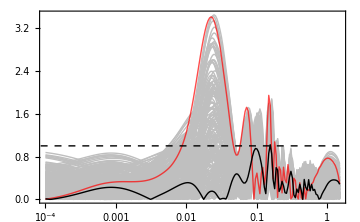

```mathematica
Module[{curves,styles,legendLabels},curves=Join[Table[AccGA[i],{i,Select[Range[Length[Params]],#!=BestFit&&#!=WorstFit&]}],{AccGA[WorstFit],AccGA[BestFit]}];
styles=Join[Table[Directive[Thin,GrayLevel[0.75]],{Length[Params]-2}],{Directive[Thick,Red,Opacity[0.7]](*Worst fit*),
Directive[Thick,Black](*Best fit*)}];
legendLabels={(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Test set}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Worst fit}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Best fit}"]};
ListLogLinearPlot[curves,Joined->True,PlotRange->{{10^-4,1.5},All},PlotStyle->styles,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"k~[h / \\text{Mpc}]","\\text{Acc}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLegends->Placed[LineLegend[styles[[-3;;]],legendLabels,LegendLayout->{"Row",3},LabelStyle->{Black,Bold,14},LegendFunction->"Frame",LegendMarkerSize->{35,15}],{0.212,0.7}],Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]}},ImageSize->Medium]//Quiet]
```

### Silk Correction

```mathematica
MockData=Drop[Drop[Join@@Table[{PkData[[j]][[i,1]],Params[[j,1]],Params[[j,2]],Params[[j,3]],Params[[j,4]],A0GA[[j]],PkData[[j]][[i,2]]},{j,Length[PkData]},{i,Length[PkData[[j]]]}],{1,-1,2}],{1,-1,2}];
```

```mathematica
(* We add a correction for the amplitude supression due to photon difussion *)
PGAsMin[k_,h_,ωb_,ωm_,ns_,A0_,A_,σs_,ks_]:=A0*k^ns*TGA[k,h,ωb,ωm]^2(1+A*ⅇ^(-((k-ks)/σs)^2))
χ2WinnerMin[A_,σs_,ks_]:=Mean[Table[Abs[1-1/MockData⟦i,7⟧PGAsMin[MockData⟦i,1⟧,MockData[[i,2]],MockData[[i,3]],MockData[[i,4]],MockData[[i,5]],MockData[[i,6]],A,σs,ks]]*100,{i,1,Length[MockData]}]];
```

```mathematica
χ2WinnerMin[0,σs,ks]
```

0.445146

```mathematica
FindMinimum[χ2WinnerMin[A,σs,ks],{{A,0.008},{σs,0.04},{ks,0.08}},MaxIterations->1000,AccuracyGoal->6,PrecisionGoal->6]//Quiet
```

{0.408242,{A→0.00837851,σs→0.0404537,ks→0.0810414}}

```mathematica
PSilkPeak2[k_]:=(1+A*ⅇ^(-((k-ks)/σs)^2))/.{A->0.008378511268703481,σs->0.0404537035946556,ks->0.08104141533171748}
```

```mathematica
(* We add a correction for the amplitude supression due to photon difussion *)
PGAsMin[k_,h_,ωb_,ωm_,ns_,A0_,A_,σs_,ks_]:=A0*k^ns*TGA[k,h,ωb,ωm]^2(1+A*ⅇ^(-((k-ks)/σs)^2))*PSilkPeak2[k];
χ2WinnerMin[A_,σs_,ks_]:=Mean[Table[Abs[1-1/MockData⟦i,7⟧PGAsMin[MockData⟦i,1⟧,MockData[[i,2]],MockData[[i,3]],MockData[[i,4]],MockData[[i,5]],MockData[[i,6]],A,σs,ks]]*100,{i,1,Length[MockData]}]]//Quiet;
```

```mathematica
FindMinimum[χ2WinnerMin[A,σs,ks],{{A,-0.01},{σs,0.005},{ks,0.15}},MaxIterations->100,AccuracyGoal->6,PrecisionGoal->6]//Quiet
```

{0.393205,{A→-0.0125386,σs→0.00758646,ks→0.143766}}

```mathematica
PSilkPeak3[k_]:=(1+A*ⅇ^(-((k-ks)/σs)^2))/.{A->-0.012538584070385451,σs->0.007586461756858841,ks->0.14376604487365813}
```

```mathematica
(* We add a correction for the amplitude supression due to photon difussion *)
PGAsMin[k_,h_,ωb_,ωm_,ns_,A0_,A_,σs_,ks_]:=A0*k^ns*TGA[k,h,ωb,ωm]^2(1+A*ⅇ^(-((k-ks)/σs)^2))*PSilkPeak2[k]*PSilkPeak3[k];
χ2WinnerMin[A_,σs_,ks_]:=Mean[Table[Abs[1-1/MockData⟦i,7⟧PGAsMin[MockData⟦i,1⟧,MockData[[i,2]],MockData[[i,3]],MockData[[i,4]],MockData[[i,5]],MockData[[i,6]],A,σs,ks]]*100,{i,1,Length[MockData]}]]//Quiet;
```

```mathematica
FindMinimum[χ2WinnerMin[A,σs,ks],{{A,-0.001},{σs,0.5},{ks,1.1}},MaxIterations->100,AccuracyGoal->6,PrecisionGoal->6]//Quiet
```

{0.384808,{A→-0.00389851,σs→0.300611,ks→1.17905}}

```mathematica
PSilkPeak4[k_]:=(1+A*ⅇ^(-((k-ks)/σs)^2))/.{A->-0.003898505712796254,σs->0.3006106056454312,ks->1.179052360594937}
```

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-A0GA[[i]]/(PkData[[i]][[j,2]])*(PkData[[i]][[j,1]])^Params[[i,4]]*TGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2*PSilkPeak2[PkData[[i]][[j,1]]]*PSilkPeak3[PkData[[i]][[j,1]]]*PSilkPeak4[PkData[[i]][[j,1]]]]},{j,Length[PkData[[i]]]}];
```

```mathematica
{Mean[#],Min[#],Max[#],Position[#,Min[#]],Position[#,Max[#]]}&@Table[Mean[AccGA[i][[All,2]]],{i,1,Length[Params]}]//Quiet
WorstFit=Position[#,Max[#]][[1,1]]&@Table[Mean[AccGA[i][[All,2]]],{i,1,Length[Params]}]//Quiet;
BestFit=Position[#,Min[#]][[1,1]]&@Table[Mean[AccGA[i][[All,2]]],{i,1,Length[Params]}]//Quiet;
```

{0.395859,0.161658,0.679074,{{57}},{{150}}}

### Visual Comparison

```mathematica
i=BestFit;j=WorstFit;
ListLogLogPlot[{PkData[[i]],PkData[[j]]},Joined->True,PlotRange->{{PkData[[1]][[50,1]],PkData[[1]][[-1,1]]},{20,5*10^4}},PlotStyle->{Directive[Thickness[0.009],Dashed,Black]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","P(k) \\, [\\text{Mpc}/h]^3 "},BaseStyle->{FontFamily->"Times",FontSize->18},ImageSize->Large];
LogLogPlot[{A0GA[[i]]*k^Params[[i,4]]*TGA[k,Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2*PSilkPeak2[k]*PSilkPeak3[k],
A0GA[[j]]*k^Params[[j,4]]*TGA[k,Params[[j,1]],Params[[j,2]],Params[[j,3]]]^2*PSilkPeak2[k]*PSilkPeak3[k]}//Evaluate,{k,10^-5,1.6},PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0.2,0.6,0.6]],Directive[Thick,RGBColor[0.9,0.1,0.4],Opacity[0.9]],Directive[Thick,RGBColor[0.3,0.6,0.2],Opacity[0.9]]},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.8]&)/@Style["\\text{Best~fit}"],
(MaTeX[#,Magnification->1.8]&)/@Style["\\text{Worst~fit}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendFunction->"Frame",LegendMarkerSize->{35,15}],
{0.25,0.2}]];
i=.;j=.;
Show[{%%%,%%}]
```

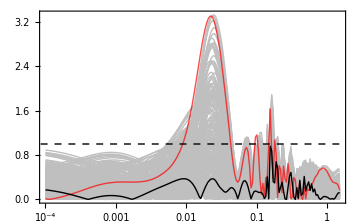

```mathematica
Module[{curves,styles,legendLabels},curves=Join[Table[AccGA[i],{i,Select[Range[Length[Params]],#!=BestFit&&#!=WorstFit&]}],{AccGA[WorstFit],AccGA[BestFit]}];
styles=Join[Table[Directive[Thin,GrayLevel[0.75]],{Length[Params]-2}],{Directive[Thick,Red,Opacity[0.7]](*Worst fit*),
Directive[Thick,Black](*Best fit*)}];
legendLabels={(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Test set}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Worst fit}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Best fit}"]};
ListLogLinearPlot[curves,Joined->True,PlotRange->{{10^-4,1.5},All},PlotStyle->styles,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"k~[h / \\text{Mpc}]","\\text{Acc}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLegends->Placed[LineLegend[styles[[-3;;]],legendLabels,LegendLayout->{"Row",3},LabelStyle->{Black,Bold,14},LegendFunction->"Frame",LegendMarkerSize->{35,15}],{0.212,0.7}],Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]}},ImageSize->Medium]//Quiet]//Quiet
```

## Correction at k_eq

```mathematica
Quit[]
```

## Error on k_eq

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[];
Off[General::munfl];
Off[General::stop];
Off[Infinity::indet];
Off[Power::infy];
Off[Indeterminate::indet];
```

### Data

```mathematica
Import["./Data/cosmo_params.txt","Table"][[1]]
Params=Import["./Data/cosmo_params.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As,sigma8}

```mathematica
dir="./Data/spectra_latin_hc/";
paths=FileNameJoin[{dir,"spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

### Fitting

```mathematica
TGAnw[k_,h_,ωb_,ωm_]:=(1+101.855 ((h*k)/(ωm-ωb))^1.483+21112.189((h*k)/(ωm-ωb))^3.972+35913.065  ((h*k)/(ωm-ωb))^6.097+1428.081((h*k)/(ωm-ωb))^7.507)^(-1/4)
TGAw[k_,h_,ωb_,ωm_]:=1+(ⅇ^(-1.36418 ((h k)/(0.373 ωb^0.419+0.195 ωm^1.0957))^0.9914) (0.10047-0.1485 ωb^0.76324+0.0005236 ωm^1.49987) Sin[(0.78991 ((h k)/(0.00785436 ωb^0.177084+0.00912388 ωm^0.618711+11.9611 ωb^2.81343 ωm^0.784719)+0.54264282715945/ωm^0.2695499))/(0.7349+1.0058717(1/(h k)(0.00785436 ωb^0.177084 ωm^0.234948+0.00912388 ωm^0.853659+11.9611 ωb^2.81343 ωm^1.019667))^1.19806)^0.739668])/(1.03922+(1/(h k)(0.00785436 ωb^0.177084+0.00912388 ωm^0.618711+11.9611 ωb^2.81343 ωm^0.784719) (1.47345-49.99978 ωb^0.96164+46.02641 ωm^1.24458))^2.7345)
TSilkPeak1[k_]:=1-0.006249*ⅇ^(-((k-0.199435)/0.062686)^2)
TGA[k_,h_,ωb_,ωm_]:=TGAnw[k,h,ωb,ωm]*TGAw[k,h,ωb,ωm]*TSilkPeak1[k]
PGA[k_,h_,ωb_,ωm_,ns_,A_]:=A*k^ns*TGA[k,h,ωb,ωm]^2
```

```mathematica
R8=8;            (*radio en Mpc/h*)
(*Función ventana top-hat*)
WtopHat[x_]:=3/x^3(Sin[x]-x Cos[x]);
σ8=Params[[All,6]];
IntegralGA[i_]:=NIntegrate[k^(Params[[i,4]]+2) TGAnw[k,Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2(WtopHat[R8*k])^2,{k,10^-5,2},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0GA=ParallelTable[2*π^2 σ8[[i]]^2/IntegralGA[i],{i,1,Length[Params]}];
```

```mathematica
MeanAccGA[A_,i_]:=Mean[Table[100*Abs[1-PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A]/(PkData[[i]][[j,2]])],{j,Length[PkData[[i]]]}]];
FindAGA=Table[FindMinimum[MeanAccGA[A,i],{A,10^6,10^7}],{i,Length[PkData]}]//Quiet;
AGA=FindAGA[[All,2,1,2]];
```

```mathematica
(*Buscar el pico numéricamente*)keqGA=ParallelTable[FindMaximum[{PGA[k,Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]],k>10^-2&&k<10^-1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6][[2,1,2]],{i,1,Length[PkData]}];
```

```mathematica
Pclass=ParallelTable[Interpolation[PkData[[i]]],{i,1,Length[PkData]}];
```

```mathematica
keqclass=ParallelTable[FindMaximum[{Pclass[[i]][k],k>10^-3&&k<1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6][[2,1,2]],{i,1,Length[Pclass]}];
```

```mathematica
Δkeq=keqclass-keqGA;
Δkf=Abs[Δkeq]/keqclass*100;
```

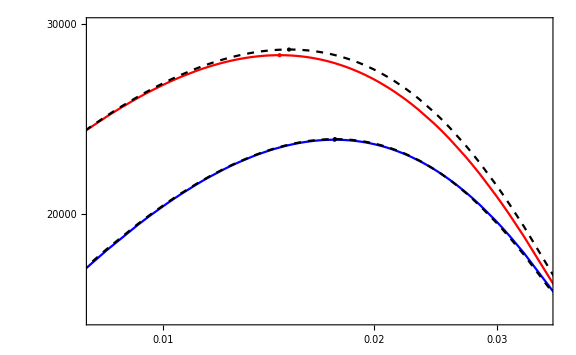

```mathematica
i=7;j=10;
Show[LogLogPlot[{PGA[k,Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]],
PGA[k,Params[[j,1]],Params[[j,2]],Params[[j,3]],Params[[j,4]],A0GA[[j]]],
Pclass[[i]][k],
Pclass[[j]][k]},{k,10^-4,1.5},PlotRange->{{0.008,0.035},{1.6*10^4,3*10^4}},PlotStyle->{Directive[Blue],Directive[Red],Directive[Black,Dashed],Directive[Black,Dashed]},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.6]&)/@Style["\\text{Best fit}"],
(MaTeX[#,Magnification->1.6]&)/@Style["\\text{Worst fit}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,15},LegendFunction->"Frame",LegendMarkerSize->{35,15}],
{0.5,0.1}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","P(k) \\, [\\text{Mpc}/h]^3 "},BaseStyle->{FontFamily->"Times",FontSize->18},ImageSize->Large],Graphics[{PointSize[Large],Blue,Point[{keqGA[[i]],PGA[keqGA[[i]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]}//Log],Red,Point[{keqGA[[j]],PGA[keqGA[[j]],Params[[j,1]],Params[[j,2]],Params[[j,3]],Params[[j,4]],A0GA[[j]]]}//Log],Black,Point[{keqclass[[i]],Pclass[[i]][keqclass[[i]]]}//Log],
Black,Point[{keqclass[[j]],Pclass[[j]][keqclass[[j]]]}//Log]}]]
i=.;j=.;
```

```mathematica
ΔAmp=Table[Abs[1-PGA[keqGA[[i]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]/(Pclass[[i]][keqclass[[i]]])]*100,{i,1,Length[PkData]}];
```

```mathematica
{ΔAmp[[7]],ΔAmp[[10]]}
{Δkf[[7]],Δkf[[10]]}
```

{0.129095,1.19577}

{0.159975,3.06179}

## Formulae: k_eq,R(k_eq),D(k_eq)

```mathematica
Quit[]
```

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
dir="./Data/Spectra_keq";
```

### k_eq

#### Varying h

```mathematica
(* Load, interpolate and find the {k,P(k)} at the maximum for each h*)MaxPkh=Table[spectrum=Import[FileNameJoin[{dir,"spectrum_h_"<>ToString[i]<>".txt"}],"Table"];
Pk=Interpolation[spectrum];
FindMaximum[{Pk[k],10^-3<k<10^-1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6],{i,0,3}];
```

```mathematica
(* Extract values of Subscript[k, eq] and P(Subscript[k, eq]) *)
hvals={0.65,0.683,0.716,0.75}
Pkeqh=MaxPkh[[All,1]]
keqh=MaxPkh[[All,2,1,2]]
```

{0.65,0.683,0.716,0.75}

{19351.8,21461.2,23666.8,25967.}

{0.01499,0.0142596,0.013596,0.0129923}

```mathematica
ListPlot[Transpose[{hvals,keqh}],Joined->True,Mesh->All,PlotStyle->{Directive[Thick,Red]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","k_\\text{eq}"},BaseStyle->{FontFamily->"Times",FontSize->18}];
ListPlot[Transpose[{hvals,Pkeqh}],Joined->True,Mesh->All,PlotStyle->{Directive[Thick,Blue]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","P(k_\\text{eq})"},BaseStyle->{FontFamily->"Times",FontSize->18}];
GraphicsRow[{%%,%},ImageSize->Full]
```

#### Varying ω_b

```mathematica
(* Load, interpolate and find the {k,P(k)} at the maximum for each Subscript[ω, b] *)MaxPkωb=Table[spectrum=Import[FileNameJoin[{dir,"spectrum_omega_b_"<>ToString[i]<>".txt"}],"Table"];
Pk=Interpolation[spectrum];
FindMaximum[{Pk[k],10^-3<k<10^-1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6],{i,0,3}];
```

```mathematica
(* Extract values of Subscript[k, eq] and P(Subscript[k, eq]) *)
ωbvals={0.0214,0.02206667,0.02273333,0.0234}
Pkeqωb=MaxPkωb[[All,1]]
keqωb=MaxPkωb[[All,2,1,2]]
```

{0.0214,0.0220667,0.0227333,0.0234}

{19351.8,19335.7,19320.,19304.9}

{0.01499,0.0149505,0.0149117,0.0148743}

```mathematica
ListPlot[Transpose[{ωbvals,keqωb}],Joined->True,Mesh->All,PlotStyle->{Directive[Thick,Red]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\omega_b","k_\\text{eq}"},BaseStyle->{FontFamily->"Times",FontSize->18}];
ListPlot[Transpose[{ωbvals,Pkeqωb}],Joined->True,Mesh->All,PlotStyle->{Directive[Thick,Blue]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\omega_b","P(k_\\text{eq})"},BaseStyle->{FontFamily->"Times",FontSize->18}];
GraphicsRow[{%%,%},ImageSize->Full]
```

#### Varying ω_m

```mathematica
(* Load, interpolate and find the {k,P(k)} at the maximum for each Subscript[ω, m] *)MaxPkωm=Table[spectrum=Import[FileNameJoin[{dir,"spectrum_omega_m_"<>ToString[i]<>".txt"}],"Table"];
Pk=Interpolation[spectrum];
FindMaximum[{Pk[k],10^-3<k<10^-1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6],{i,0,3}];
```

```mathematica
(* Extract values of Subscript[k, eq] and P(Subscript[k, eq]) *)
ωmvals={0.13,0.13666667,0.14333333,0.15}
Pkeqωm=MaxPkωm[[All,1]]
keqωm=MaxPkωm[[All,2,1,2]]
```

{0.13,0.136667,0.143333,0.15}

{19351.8,18716.8,18127.6,17578.9}

{0.01499,0.015665,0.0163381,0.0170115}

```mathematica
ListPlot[Transpose[{ωmvals,keqωm}],Joined->True,Mesh->All,PlotStyle->{Directive[Thick,Red]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\omega_m","k_\\text{eq}"},BaseStyle->{FontFamily->"Times",FontSize->18}];
ListPlot[Transpose[{ωmvals,Pkeqωm}],Joined->True,Mesh->All,PlotStyle->{Directive[Thick,Blue]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\omega_m","P(k_\\text{eq})"},BaseStyle->{FontFamily->"Times",FontSize->18}];
GraphicsRow[{%%,%},ImageSize->Full]
```

#### Varying n_s

```mathematica
(* Load, interpolate and find the {k,P(k)} at the maximum for each Subscript[n, s] *)MaxPkns=Table[spectrum=Import[FileNameJoin[{dir,"spectrum_ns_"<>ToString[i]<>".txt"}],"Table"];
Pk=Interpolation[spectrum];
FindMaximum[{Pk[k],10^-3<k<10^-1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6],{i,0,3}];
```

```mathematica
(* Extract values of Subscript[k, eq] and P(Subscript[k, eq]) *)
nsvals={0.9,0.93333333,0.96666667,1.}
Pkeqns=MaxPkns[[All,1]]
keqns=MaxPkns[[All,2,1,2]]
```

{0.9,0.933333,0.966667,1.}

{19351.8,18335.5,17392.1,16515.1}

{0.01499,0.0155105,0.01603,0.0165486}

```mathematica
ListPlot[Transpose[{nsvals,keqns}],Joined->True,Mesh->All,PlotStyle->{Directive[Thick,Red]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"n_s","k_\\text{eq}"},BaseStyle->{FontFamily->"Times",FontSize->18}];
ListPlot[Transpose[{nsvals,Pkeqns}],Joined->True,Mesh->All,PlotStyle->{Directive[Thick,Blue]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"n_s","P(k_\\text{eq})"},BaseStyle->{FontFamily->"Times",FontSize->18}];
GraphicsRow[{%%,%},ImageSize->Full]
```

#### Varying A_s

```mathematica
(* Load, interpolate and find the {k,P(k)} at the maximum for each Subscript[A, s] *)MaxPkAs=Table[spectrum=Import[FileNameJoin[{dir,"spectrum_As_"<>ToString[i]<>".txt"}],"Table"];
Pk=Interpolation[spectrum];
FindMaximum[{Pk[k],10^-3<k<10^-1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6],{i,0,3}];
```

```mathematica
(* Extract values of Subscript[k, eq] and P(Subscript[k, eq]) *)
Asvals={1.5,1.83333333,2.16666667,2.5}
PkeqAs=MaxPkAs[[All,1]]
keqAs=MaxPkAs[[All,2,1,2]]
```

{1.5,1.83333,2.16667,2.5}

{19351.8,23652.1,27952.5,32252.9}

{0.01499,0.01499,0.01499,0.01499}

```mathematica
ListPlot[Transpose[{Asvals,keqAs}],Joined->True,Mesh->All,PlotStyle->{Directive[Thick,Red]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"A_s","k_\\text{eq}"},BaseStyle->{FontFamily->"Times",FontSize->18}];
ListPlot[Transpose[{Asvals,PkeqAs}],Joined->True,Mesh->All,PlotStyle->{Directive[Thick,Blue]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"A_s","P(k_\\text{eq})"},BaseStyle->{FontFamily->"Times",FontSize->18}];
GraphicsRow[{%%,%},ImageSize->Full]
```

#### Varying A_s

```mathematica
SpectrumAs0=Import[dir<>"/spectrum_As_0.txt","Table"];
SpectrumAs1=Import[dir<>"/spectrum_As_1.txt","Table"];
SpectrumAs2=Import[dir<>"/spectrum_As_2.txt","Table"];
SpectrumAs3=Import[dir<>"/spectrum_As_3.txt","Table"];
```

```mathematica
PkAs0=Interpolation[SpectrumAs0];
PkAs1=Interpolation[SpectrumAs1];
PkAs2=Interpolation[SpectrumAs2];
PkAs3=Interpolation[SpectrumAs3];
```

```mathematica
FindMaximum[{PkAs0[k],k>10^-3&&k<10^-1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6];
PkeqAs0=%[[1]]
keqAs0=%%[[2,1,2]]
```

19351.8

0.01499

```mathematica
FindMaximum[{PkAs1[k],k>10^-3&&k<10^-1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6];
PkeqAs1=%[[1]]
keqAs1=%%[[2,1,2]]
```

23652.1

0.01499

```mathematica
FindMaximum[{PkAs2[k],k>10^-3&&k<10^-1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6];
PkeqAs2=%[[1]]
keqAs2=%%[[2,1,2]]
```

27952.5

0.01499

```mathematica
FindMaximum[{PkAs3[k],k>10^-3&&k<10^-1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6];
PkeqAs3=%[[1]]
keqAs3=%%[[2,1,2]]
```

32252.9

0.01499

```mathematica
Asvals={1.5,1.83333333,2.16666667,2.5}
keqAs=Join[{keqAs0,keqAs1,keqAs2,keqAs3}]
PkeqAs=Join[{PkeqAs0,PkeqAs1,PkeqAs2,PkeqAs3}]
```

{1.5,1.83333,2.16667,2.5}

{0.01499,0.01499,0.01499,0.01499}

{19351.8,23652.1,27952.5,32252.9}

```mathematica
ListPlot[Transpose[{Asvals,keqAs}],Joined->True,Mesh->All];
ListPlot[Transpose[{Asvals,PkeqAs}],Joined->True,Mesh->All];
GraphicsRow[{%%,%},ImageSize->Full]
```

#### Analytical Approximation

```mathematica
(* Function to build arrays varying one parameter at a time *)
varyList[list_,refValue_,paramPos_]:=Table[ReplacePart[{hvals[[1]],ωbvals[[1]],ωmvals[[1]],nsvals[[1]],Asvals[[1]]},paramPos->list[[i]]],{i,1,Length[list]}];
(* Create sublists with the variation of each parameter *)subdataPkeqh=MapThread[Append,{varyList[hvals,hvals[[1]],1],Pkeqh}];
subdataPkeqωb=MapThread[Append,{varyList[ωbvals,ωbvals[[1]],2],Pkeqωb}];
subdataPkeqωm=MapThread[Append,{varyList[ωmvals,ωmvals[[1]],3],Pkeqωm}];
subdataPkeqns=MapThread[Append,{varyList[nsvals,nsvals[[1]],4],Pkeqns}];
subdataPkeqAs=MapThread[Append,{varyList[Asvals,Asvals[[1]],5],PkeqAs}];
(* Join everything in one dataset *)DataSetPkeq=Join[subdataPkeqh,subdataPkeqωb,subdataPkeqωm,subdataPkeqns,subdataPkeqAs];
```

```mathematica
(* Ansatz for P(Subscript[k, eq]) *)
PkeqAnalytical[h_,ωb_,ωm_,ns_,As_,Amp_,a1_,a2_,a3_,a4_]:=Amp*10^4*(h^a1 ⅇ^(-a2*ωb))/(ωm^a3*ns^a4)*As
```

```mathematica
χPkeq[Amp_,a1_,a2_,a3_,a4_]:=Mean[Table[Abs[(1-1/DataSetPkeq[[i,6]] PkeqAnalytical[DataSetPkeq[[i,1]],DataSetPkeq[[i,2]],DataSetPkeq[[i,3]],DataSetPkeq[[i,4]],DataSetPkeq[[i,5]],Amp,a1,a2,a3,a4])]*100,{i,1,Length[DataSetPkeq]}]]
```

```mathematica
NMinimize[χPkeq[Amp,a1,a2,a3,a4],{Amp,a1,a2,a3,a4},Method->"DifferentialEvolution",AccuracyGoal->6,PrecisionGoal->6,MaxIterations->50000]
ParamsPkeq=%[[2]]
```

{0.0307961,{Amp→0.708094,a1→2.08143,a2→1.23033,a3→0.669274,a4→1.49408}}

{Amp→0.708094,a1→2.08143,a2→1.23033,a3→0.669274,a4→1.49408}

```mathematica
i=20;
PkeqAnalytical[DataSetPkeq[[i,1]],DataSetPkeq[[i,2]],DataSetPkeq[[i,3]],DataSetPkeq[[i,4]],DataSetPkeq[[i,5]],Amp,a1,a2,a3,a4]/.ParamsPkeq
DataSetPkeq[[i,6]]
i=.;
```

32252.9

32252.9

```mathematica
(* Function to build arrays varying one parameter at a time *)
varyList[list_,refValue_,paramPos_]:=Table[ReplacePart[{hvals[[1]],ωbvals[[1]],ωmvals[[1]],nsvals[[1]]},paramPos->list[[i]]],{i,1,Length[list]}];
(* Create sublists with the variation of each parameter *)subdatakeqh=MapThread[Append,{varyList[hvals,hvals[[1]],1],keqh}];
subdatakeqωb=MapThread[Append,{varyList[ωbvals,ωbvals[[1]],2],keqωb}];
subdatakeqωm=MapThread[Append,{varyList[ωmvals,ωmvals[[1]],3],keqωm}];
subdatakeqns=MapThread[Append,{varyList[nsvals,nsvals[[1]],4],keqns}];
(* Join everything in one dataset *)
DataSetkeq=Join[subdatakeqh,subdatakeqωb,subdatakeqωm,subdatakeqns];
```

```mathematica
(* Ansatz for Subscript[k, eq] *)
keqAnalytical[h_,ωb_,ωm_,ns_,A_,a1_,a2_,a3_,a4_,a5_]:=A*(ωm^a1*ns^a2)/(h^a3*(1+a4*ωb)^a5)
```

```mathematica
χkeq[A_,a1_,a2_,a3_,a4_,a5_]:=Mean[Table[Abs[1-1/DataSetkeq[[i,5]](keqAnalytical[DataSetkeq[[i,1]],DataSetkeq[[i,2]],DataSetkeq[[i,3]],DataSetkeq[[i,4]],A,a1,a2,a3,a4,a5])]*100,{i,Length[DataSetkeq]}]]
```

```mathematica
NMinimize[χkeq[A,a1,a2,a3,a4,a5],{A,a1,a2,a3,a4,a5},Method->"DifferentialEvolution",AccuracyGoal->6,PrecisionGoal->6,MaxIterations->10000]
Paramskeq=%[[2]]
```

{0.011852,{A→0.0706619,a1→0.882421,a2→0.939057,a3→1.00649,a4→1.20249,a5→3.33952}}

{A→0.0706619,a1→0.882421,a2→0.939057,a3→1.00649,a4→1.20249,a5→3.33952}

```mathematica
i=5;
keqAnalytical[DataSetkeq[[i,1]],DataSetkeq[[i,2]],DataSetkeq[[i,3]],DataSetkeq[[i,4]],A,a1,a2,a3,a4]/.Paramskeq
DataSetkeq[[i,5]]
i=.;
```

0.01499

0.01499

```mathematica
PkeqAnalytical[h,ωb,ωm,ns,As,Amp,a1,a2,a3,a4]/.ParamsPkeq
keqAnalytical[h,ωb,ωm,ns,A,a1,a2,a3,a4,a5]/.Paramskeq
```

(7080.94 As ⅇ^(-1.23033 ωb) h^2.08143)/(ns^1.49408 ωm^0.669274)

(0.0706619 ns^0.939057 ωm^0.882421)/(h^1.00649 (1+1.20249 ωb)^3.33952)

#### Test

```mathematica
dir="/Users/cosmology/Projects/Wiggles Project/Wiggles_Project/Data/";
```

```mathematica
Import["./Data/cosmo_params.txt","Table"][[1]]
Params=Import["./Data/cosmo_params.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As}

```mathematica
paths=FileNameJoin[{"./Data/spectra_latin_hc/spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

```mathematica
Pclass=ParallelTable[Interpolation[PkData[[i]]],{i,1,Length[PkData]}];
```

```mathematica
Pkeqclass=ParallelTable[FindMaximum[{Pclass[[i]][k],k>10^-3&&k<1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6][[1]],{i,1,Length[Pclass]}];
```

```mathematica
keqclass=ParallelTable[FindMaximum[{Pclass[[i]][k],k>10^-3&&k<1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6][[2,1,2]],{i,1,Length[Pclass]}];
```

```mathematica
Pkeq[h_,ωb_,ωm_,ns_,As_]:=(7080.944As ⅇ^(-1.230ωb) h^("2.081"))/(ns^1.5 ωm^("0.669"))
keq[h_,ωb_,ωm_,ns_]:=(0.07066 ns^0.939 ωm^0.8824)/(h^1.00649 (1+1.2025 ωb)^3.3395)
```

```mathematica
TestPkeq=Table[Abs[1-Pkeq[Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]]]/Pkeqclass[[i]]]*100,{i,1,Length[PkData]}];
{Mean[#],Min[#],Max[#]}&@TestPkeq
```

{0.240443,0.0016015,0.92049}

```mathematica
Testkeq=Table[Abs[1-keq[Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]]]/keqclass[[i]]]*100,{i,1,Length[PkData]}];
{Min[#],Max[#],Mean[#],Position[#,Min[#]][[1,1]],Position[#,Max[#]][[1,1]],Params[[Position[#,Min[#]][[1,1]]]],Params[[Position[#,Max[#]][[1,1]]]]}&@Testkeq
```

{0.000525528,0.152312,0.0445534,19,75,{0.677309,0.0218764,0.140521,0.918994,1.93738},{0.685619,0.0233265,0.146559,0.981647,1.92457}}

### R(k_eq) = P_Class(k_eq)/P_GA(k_eq)

#### Fitting Function

```mathematica
TGAnw[k_,h_,ωb_,ωm_]:=(1+101.855 ((h*k)/(ωm-ωb))^1.483+21112.189((h*k)/(ωm-ωb))^3.972+35913.065  ((h*k)/(ωm-ωb))^6.097+1428.081((h*k)/(ωm-ωb))^7.507)^(-1/4)
TGAw[k_,h_,ωb_,ωm_]:="1"+(ⅇ^("-1.364" ((h k)/("0.373" ωb^("0.419")+"0.195" ωm^("1.096")))^("0.991")) ("0.100"-"0.149" ωb^("0.763")+"0.001" ωm^("1.500")) Sin[("0.790" ((h k)/("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785"))+("0.543")/ωm^("0.270")))/(("0.735"+"1.006" (("0.008" ωb^("0.177") ωm^("0.235")+"0.009" ωm^("0.854")+"11.961" ωb^("2.813") ωm^("1.020"))/(h k))^("1.198"))^("0.740"))])/("1.039"+((("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785")) ("1.473"-"50.000" ωb^("0.962")+"46.026" ωm^("1.245")))/(h k))^("2.735")) 
Tsilk[k_]:=1-0.00625*ⅇ^(-((k-0.199)/0.0627)^2)
TGA[k_,h_,ωb_,ωm_]:=TGAnw[k,h,ωb,ωm]*TGAw[k,h,ωb,ωm]*Tsilk[k]
(*Espectro de potencias teórico*)
PGA[k_,h_,ωb_,ωm_,ns_,A_]:=A*k^ns*TGA[k,h,ωb,ωm]^2
keq[h_,ωb_,ωm_,ns_]:=(0.07066 ns^0.939 ωm^0.8824)/(h^1.00649 (1+1.2025 ωb)^3.3395)
```

#### Parameters

```mathematica
dir="./Data/Spectra_keq";
```

```mathematica
hvals={0.65,0.683,0.716,0.75};
ωbvals={0.0214,0.02206667,0.02273333,0.0234};
ωmvals={0.13,0.13666667,0.14333333,0.15};
nsvals={0.9,0.93333333,0.96666667,1.};
Asvals={1.5,1.83333333,2.16666667,2.5};
href=hvals[[1]];
ωbref=ωbvals[[1]];
ωmref=ωmvals[[1]];
nsref=nsvals[[1]];
Asref=Asvals[[1]];
```

#### Varying h

```mathematica
(*Paso 1:Definir los espectros y parámetros*)spectrah=Table[Import[dir<>"/spectrum_h_"<>ToString[i]<>".txt","Table"],{i,0,3}];
(*Paso 3:Crear función para minimizar el error y obtener AGAh*)
getAh[spectrum_,h_]:=Module[{res},res=FindMinimum[Mean[Table[100*Abs[1-PGA[spectrum[[i,1]],h,ωbref,ωmref,nsref,A0]/spectrum[[i,2]]],{i,Length[spectrum]}]],{A0,10^6,10^7}];
A0/. Last[res]]
(*Paso 4:Aplicar sobre todos los espectros*)
Ah=Table[getAh[spectrah[[i]],hvals[[i]]],{i,1,4}]
```

{1.92413×10^6,2.23284×10^6,2.56858×10^6,2.94073×10^6}

```mathematica
Pkeqh={19351.75740186385,21461.2314028837,23666.80354373347,25966.97828352941};
```

```mathematica
Reqh=Table[Pkeqh[[i]]/PGA[keqh[[i]],hvals[[i]],ωbref,ωmref,nsref,Ah[[i]]],{i,1,4}]
```

{1.00716,1.00638,1.00658,1.00581}

#### Varying ω_b

```mathematica
(*Paso 1:Definir los espectros y parámetros*)spectraωb=Table[Import[dir<>"/spectrum_omega_b_"<>ToString[i]<>".txt","Table"],{i,0,3}];
(*Paso 3:Crear función para minimizar el error y obtener AGAh*)
getAωb[spectrum_,ωb_]:=Module[{res},res=FindMinimum[Mean[Table[100*Abs[1-PGA[spectrum[[i,1]],href,ωb,ωmref,nsref,A0]/spectrum[[i,2]]],{i,Length[spectrum]}]],{A0,10^6,10^7}];
A0/. Last[res]]
(*Paso 4:Aplicar sobre todos los espectros*)
Aωb=Table[getAωb[spectraωb[[i]],ωbvals[[i]]],{i,1,4}]
```

{1.92413×10^6,1.92407×10^6,1.92456×10^6,1.92499×10^6}

```mathematica
Pkeqωb={19351.75740186385,19335.68346904537,19320.038163920974,19304.885142388353};
```

```mathematica
Reqωb=Table[Pkeqωb[[i]]/PGA[keqωb[[i]],href,ωbvals[[i]],ωmref,nsref,Aωb[[i]]],{i,1,4}]
```

{1.00716,1.01203,1.01671,1.02151}

#### Varying ω_m

```mathematica
(*Paso 1:Definir los espectros y parámetros*)spectraωm=Table[Import[dir<>"/spectrum_omega_m_"<>ToString[i]<>".txt","Table"],{i,0,3}];
(*Paso 3:Crear función para minimizar el error y obtener AGAh*)
getAωm[spectrum_,ωm_]:=Module[{res},res=FindMinimum[Mean[Table[100*Abs[1-PGA[spectrum[[i,1]],href,ωbref,ωm,nsref,A0]/spectrum[[i,2]]],{i,Length[spectrum]}]],{A0,10^6,10^7}];
A0/. Last[res]]
(*Paso 4:Aplicar sobre todos los espectros*)
Aωm=Table[getAωm[spectraωm[[i]],ωmvals[[i]]],{i,1,4}]
```

{1.92413×10^6,1.78048×10^6,1.65293×10^6,1.53972×10^6}

```mathematica
Pkeqωm={19351.75740186385,18716.795212632413,18127.613923788118,17578.916633565903};
```

```mathematica
Reqωm=Table[Pkeqωm[[i]]/PGA[keqωm[[i]],href,ωbref,ωmvals[[i]],nsref,Aωm[[i]]],{i,1,4}]
```

{1.00716,0.99791,0.990048,0.982937}

#### Varying n_s

```mathematica
(*Paso 1:Definir los espectros y parámetros*)spectrans=Table[Import[dir<>"/spectrum_ns_"<>ToString[i]<>".txt","Table"],{i,0,3}];
(*Paso 3:Crear función para minimizar el error y obtener AGAh*)
getAns[spectrum_,ns_]:=Module[{res},res=FindMinimum[Mean[Table[100*Abs[1-PGA[spectrum[[i,1]],href,ωbref,ωmref,ns,A0]/spectrum[[i,2]]],{i,Length[spectrum]}]],{A0,10^6,10^7}];
A0/. Last[res]]
(*Paso 4:Aplicar sobre todos los espectros*)
Ans=Table[getAns[spectrans[[i]],nsvals[[i]]],{i,1,4}]
```

{1.92413×10^6,2.09588×10^6,2.28295×10^6,2.48673×10^6}

```mathematica
Pkeqns={19351.75740186385,18335.547598575802,17392.133074532827,16515.06075424116};
```

```mathematica
Reqns=Table[Pkeqns[[i]]/PGA[keqns[[i]],href,ωbref,ωmref,nsvals[[i]],Ans[[i]]],{i,1,4}]
```

{1.00716,1.00819,1.00921,1.01023}

#### Varying A_s

```mathematica
(*Paso 1:Definir los espectros y parámetros*)spectraAs=Table[Import[dir<>"/spectrum_As_"<>ToString[i]<>".txt","Table"],{i,0,3}];
(*Paso 3:Crear función para minimizar el error y obtener AGAh*)
getAAs[spectrum_,As_]:=Module[{res},res=FindMinimum[Mean[Table[100*Abs[1-PGA[spectrum[[i,1]],href,ωbref,ωmref,nsref,A0]/spectrum[[i,2]]],{i,Length[spectrum]}]],{A0,10^6,10^7}];
A0/. Last[res]]
(*Paso 4:Aplicar sobre todos los espectros*)
AAs=Table[getAAs[spectraAs[[i]],Asvals[[i]]],{i,1,4}]
```

{1.92413×10^6,2.35171×10^6,2.7793×10^6,3.20688×10^6}

```mathematica
PkeqAs={19351.75740186385,23652.148011286354,27952.538522594637,32252.92903808056};
```

```mathematica
ReqAs=Table[PkeqAs[[i]]/PGA[keq[href,ωbref,ωmref,nsref],href,ωbref,ωmref,nsref,AAs[[i]]],{i,1,4}]
```

{1.00716,1.00716,1.00716,1.00716}

#### Analytical Approximation

```mathematica
Reqh
Reqωb
Reqωm
Reqns
ReqAs
```

{1.00716,1.00638,1.00658,1.00581}

{1.00716,1.01203,1.01671,1.02151}

{1.00716,0.99791,0.990048,0.982937}

{1.00716,1.00819,1.00921,1.01023}

{1.00716,1.00716,1.00716,1.00716}

```mathematica
(*Función para construir las listas con una variación a la vez*)
varyList[list_,refValue_,paramPos_]:=Table[ReplacePart[{hvals[[1]],ωbvals[[1]],ωmvals[[1]],nsvals[[1]]},paramPos->list[[i]]],{i,1,Length[list]}];
(*Crear sublistas con la variación de cada parámetro*)subdataReqh=MapThread[Append,{varyList[hvals,hvals[[1]],1],Reqh}];
subdataReqωb=MapThread[Append,{varyList[ωbvals,ωbvals[[1]],2],Reqωb}];
subdataReqωm=MapThread[Append,{varyList[ωmvals,ωmvals[[1]],3],Reqωm}];
subdataReqns=MapThread[Append,{varyList[nsvals,nsvals[[1]],4],Reqns}];
(*Unir Rodo en un solo dataset*)
DataSetReq=Join[subdataReqh,subdataReqωb,subdataReqωm,subdataReqns];
```

```mathematica
ReqAnalytical[h_,ωb_,ωm_,ns_,a1_,a2_,a3_,a4_,a5_]:=a1+a2*h^2+a3*ωb+a4/ωm+a5*ns
```

```mathematica
χkeq[a1_,a2_,a3_,a4_,a5_]:=Mean[Table[Abs[1-(ReqAnalytical[DataSetReq[[i,1]],DataSetReq[[i,2]],DataSetReq[[i,3]],DataSetReq[[i,4]],a1,a2,a3,a4,a5]/DataSetReq[[i,5]])]*100,{i,Length[DataSetReq]}]]
```

```mathematica
NMinimize[χkeq[a1,a2,a3,a4,a5],{a1,a2,a3,a4,a5},Method->"DifferentialEvolution",AccuracyGoal->6,PrecisionGoal->6,MaxIterations->10000]
ParamsReq=%[[2]]
```

{0.00842741,{a1→0.646093,a2→-0.00970801,a3→7.17281,a4→0.0239205,a5→0.0307467}}

{a1→0.646093,a2→-0.00970801,a3→7.17281,a4→0.0239205,a5→0.0307467}

```mathematica
Req[h_,ωb_,ωm_,ns_]:=a1+a2*h^2+a3*ωb+a4/ωm+a5*ns/.ParamsReq
NumberForm[Req[h,ωb,ωm,ns],{Infinity,4}]
```

0.6461-0.0097 h^2+0.0307 ns+7.1728 ωb+0.0239/ωm

```mathematica
i=3;
Req[DataSetReq[[i,1]],DataSetReq[[i,2]],DataSetReq[[i,3]],DataSetReq[[i,4]]]
DataSetReq[[i,5]]
i=.;
```

1.00629

1.00658

#### Test

```mathematica
Import["./Data/cosmo_params.txt","Table"][[1]]
Params=Import["./Data/cosmo_params.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As}

```mathematica
paths=FileNameJoin[{"./Data/spectra_latin_hc/spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

```mathematica
Pclass=ParallelTable[Interpolation[PkData[[i]]],{i,1,Length[PkData]}];
```

```mathematica
Pkeqclass=ParallelTable[FindMaximum[{Pclass[[i]][k],k>10^-3&&k<1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6][[1]],{i,1,Length[Pclass]}];
keqclass=ParallelTable[FindMaximum[{Pclass[[i]][k],k>10^-3&&k<1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6][[2,1,2]],{i,1,Length[Pclass]}];
```

```mathematica
MeanAccGA[A_,i_]:=Mean[Table[100*Abs[1-PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A]/(PkData[[i]][[j,2]])],{j,Length[PkData[[i]]]}]];
FindAGA=ParallelTable[FindMinimum[MeanAccGA[A,i],{A,10^6,10^7}],{i,Length[PkData]}]//Quiet;
AGA=FindAGA[[All,2,1,2]]//Quiet;
{Mean[#],Min[#],Max[#]}&@FindAGA[[All,1]]//Quiet
(* At this point, the formula is 0.37% accurate on average *)
```

{0.372242,0.21991,0.707054}

```mathematica
ReqNum[i_]:=Pkeqclass[[i]]/PGA[keqclass[[i]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],AGA[[i]]]
Req[h_,ωb_,ωm_,ns_]:="0.6461"-"0.0097" h^("2")+"0.0307" ns+"7.1728" ωb+("0.0239")/ωm
```

```mathematica
TestReq=Table[Abs[1-Req[Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]]]/ReqNum[i]]*100,{i,1,Length[PkData]}];
{Mean[#],Min[#],Max[#]}&@TestReq
```

{0.0891973,0.00438987,0.31862}

### P_GA(k_eq), P_GA'(k_eq)

#### Fitting Function

```mathematica
TGAnw[k_,h_,ωb_,ωm_]:=(1+101.855 ((h*k)/(ωm-ωb))^1.483+21112.189((h*k)/(ωm-ωb))^3.972+35913.065  ((h*k)/(ωm-ωb))^6.097+1428.081((h*k)/(ωm-ωb))^7.507)^(-1/4)
TGAw[k_,h_,ωb_,ωm_]:="1"+(ⅇ^("-1.364" ((h k)/("0.373" ωb^("0.419")+"0.195" ωm^("1.096")))^("0.991")) ("0.100"-"0.149" ωb^("0.763")+"0.001" ωm^("1.500")) Sin[("0.790" ((h k)/("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785"))+("0.543")/ωm^("0.270")))/(("0.735"+"1.006" (("0.008" ωb^("0.177") ωm^("0.235")+"0.009" ωm^("0.854")+"11.961" ωb^("2.813") ωm^("1.020"))/(h k))^("1.198"))^("0.740"))])/("1.039"+((("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785")) ("1.473"-"50.000" ωb^("0.962")+"46.026" ωm^("1.245")))/(h k))^("2.735")) 
Tsilk[k_]:=1-0.00625*ⅇ^(-((k-0.199)/0.0627)^2)
TGA[k_,h_,ωb_,ωm_]:=TGAnw[k,h,ωb,ωm]*TGAw[k,h,ωb,ωm]*Tsilk[k]
(*Espectro de potencias teórico*)
PGA[k_,h_,ωb_,ωm_,ns_,A_]:=A*k^ns*TGA[k,h,ωb,ωm]^2
DPGA[k_,h_,ωb_,ωm_,ns_,A_]=D[PGA[k,h,ωb,ωm,ns,A],k];
Deqnw[h_,ωb_,ωm_,ns_]:=(ns/k+2D[Log[TGA[k,h,ωb,ωm]],k])/.k->keq[h,ωb,ωm,ns]
keq[h_,ωb_,ωm_,ns_]:=(0.07066 ns^0.939 ωm^0.8824)/(h^1.00649 (1+1.2025 ωb)^3.3395)
```

#### Varying Parameters

```mathematica
hvals={0.65,0.683,0.716,0.75};
ωbvals={0.0214,0.02206667,0.02273333,0.0234};
ωmvals={0.13,0.13666667,0.14333333,0.15};
nsvals={0.9,0.93333333,0.96666667,1.};
Asvals={1.5,1.83333333,2.16666667,2.5};
href=hvals[[1]];
ωbref=ωbvals[[1]];
ωmref=ωmvals[[1]];
nsref=nsvals[[1]];
Asref=Asvals[[1]];
```

```mathematica
PGAkeqh=Table[PGA[keq[hvals[[i]],ωbref,ωmref,nsref],hvals[[i]],ωbref,ωmref,nsref,A]/A,{i,1,4}]
PGAkeqωb=Table[PGA[keq[href,ωbvals[[i]],ωmref,nsref],href,ωbvals[[i]],ωmref,nsref,A]/A,{i,1,4}]
PGAkeqωm=Table[PGA[keq[href,ωbref,ωmvals[[i]],nsref],href,ωbref,ωmvals[[i]],nsref,A]/A,{i,1,4}]
PGAkeqns=Table[PGA[keq[href,ωbref,ωmref,nsvals[[i]]],href,ωbref,ωmref,nsvals[[i]],A]/A,{i,1,4}]
```

{0.00998586,0.00955065,0.00915364,0.00877939}

{0.00998586,0.00992987,0.00987372,0.00981743}

{0.00998586,0.0105342,0.0110772,0.0116151}

{0.00998586,0.00867732,0.00754869,0.00657401}

```mathematica
DPGAkeqh=Table[DPGA[keq[hvals[[i]],ωbref,ωmref,nsref],hvals[[i]],ωbref,ωmref,nsref,A]/A,{i,1,4}]
DPGAkeqωb=Table[DPGA[keq[href,ωbvals[[i]],ωmref,nsref],href,ωbvals[[i]],ωmref,nsref,A]/A,{i,1,4}]
DPGAkeqωm=Table[DPGA[keq[href,ωbref,ωmvals[[i]],nsref],href,ωbref,ωmvals[[i]],nsref,A]/A,{i,1,4}]
DPGAkeqns=Table[DPGA[keq[href,ωbref,ωmref,nsvals[[i]]],href,ωbref,ωmref,nsvals[[i]],A]/A,{i,1,4}]
```

{-0.0194663,-0.0193553,-0.019248,-0.0191411}

{-0.0194663,-0.0214855,-0.0235218,-0.0255749}

{-0.0194663,-0.010866,-0.00289821,0.00451247}

{-0.0194663,-0.0169866,-0.0147425,-0.0127229}

#### Analytical Approximation

```mathematica
(*Función para construir las listas con una variación a la vez*)
varyList[list_,refValue_,paramPos_]:=Table[ReplacePart[{hvals[[1]],ωbvals[[1]],ωmvals[[1]],nsvals[[1]]},paramPos->list[[i]]],{i,1,Length[list]}];
(*Crear sublistas con la variación de cada parámetro*)subdataPGAkeqh=MapThread[Append,{varyList[hvals,hvals[[1]],1],PGAkeqh}];
subdataPGAkeqωb=MapThread[Append,{varyList[ωbvals,ωbvals[[1]],2],PGAkeqωb}];
subdataPGAkeqωm=MapThread[Append,{varyList[ωmvals,ωmvals[[1]],3],PGAkeqωm}];
subdataPGAkeqns=MapThread[Append,{varyList[nsvals,nsvals[[1]],4],PGAkeqns}];
(*Unir todo en un solo dataset*)
DataSetPGAkeq=Join[subdataPGAkeqh,subdataPGAkeqωb,subdataPGAkeqωm,subdataPGAkeqns];
```

```mathematica
PGAkeq[h_,ωb_,ωm_,ns_,Amp_,a1_,a2_,a3_,a4_]:=Amp*(h^a1 ⅇ^(-a2*ωb))/(ωm^a3*ns^a4)
```

```mathematica
χPGAkeq[Amp_,a1_,a2_,a3_,a4_]:=Mean[Table[Abs[(1-1/DataSetPGAkeq[[i,5]] PGAkeq[DataSetPGAkeq[[i,1]],DataSetPGAkeq[[i,2]],DataSetPGAkeq[[i,3]],DataSetPGAkeq[[i,4]],Amp,a1,a2,a3,a4])]*100,{i,1,Length[DataSetPGAkeq]}]]
```

```mathematica
NMinimize[χPGAkeq[Amp,a1,a2,a3,a4],{Amp,a1,a2,a3,a4},Method->"DifferentialEvolution",AccuracyGoal->6,PrecisionGoal->6,MaxIterations->10000]
ParamsPGAkeq=%[[2]]
```

{0.0547885,{Amp→0.0470031,a1→-0.89981,a2→8.50419,a3→-1.06224,a4→3.91548}}

{Amp→0.0470031,a1→-0.89981,a2→8.50419,a3→-1.06224,a4→3.91548}

```mathematica
i=3;
PGAkeq[DataSetPGAkeq[[i,1]],DataSetPGAkeq[[i,2]],DataSetPGAkeq[[i,3]],DataSetPGAkeq[[i,4]],Amp,a1,a2,a3,a4]/.ParamsPGAkeq
DataSetPGAkeq[[i,5]]
i=.;
```

0.00915364

0.00915364

```mathematica
(*Crear sublistas con la variación de cada parámetro*)subdataDPGAkeqh=MapThread[Append,{varyList[hvals,hvals[[1]],1],DPGAkeqh}];
subdataDPGAkeqωb=MapThread[Append,{varyList[ωbvals,ωbvals[[1]],2],DPGAkeqωb}];
subdataDPGAkeqωm=MapThread[Append,{varyList[ωmvals,ωmvals[[1]],3],DPGAkeqωm}];
subdataDPGAkeqns=MapThread[Append,{varyList[nsvals,nsvals[[1]],4],DPGAkeqns}];
(*Unir todo en un solo dataset*)
DataSetDPGAkeq=Join[subdataDPGAkeqh,subdataDPGAkeqωb,subdataDPGAkeqωm,subdataDPGAkeqns];
```

```mathematica
X=DataSetDPGAkeq[[All,;;4]];   (*Input parameters*)
Y=DataSetDPGAkeq[[All,-1]];     (*True values*)
lm=LinearModelFit[DataSetDPGAkeq,{1,h,h^2,ωb, ωb^2,ωm,ωm^2,ns,ns^2},{h,ωb,ωm,ns}];
%["RSquared"]
DPGAkeq[h_,ωb_,ωm_,ns_]=%%["BestFit"]
```

1.

-0.40649+0.00518334 h-0.00138667 h^2+0.263882 ns-0.103402 ns^2-2.22729 ωb-18.4715 ωb^2+3.0768 ωm-6.70755 ωm^2

```mathematica
DataSetDPGAkeq[[All,;;4]]//Length
```

16

```mathematica
MSE=Mean[Table[(DPGAkeq@@X[[i]]-Y[[i]])^2,{i,1,Length[X]}]]
MAE=Mean[Table[Abs[DPGAkeq@@X[[i]]-Y[[i]]],{i,1,Length[X]}]]
MPE=Mean[Table[100*Abs[1-(DPGAkeq@@X[[i]])/Y[[i]]],{i,Length[X]}]]
```

1.87791×10^-11

2.24701×10^-6

0.0405251

```mathematica
i=6;
DPGAkeq@@X[[i]]
DataSetDPGAkeq[[i,5]]
i=.;
```

-0.0214854

-0.0214855

```mathematica
PGAkeq[h,ωb,ωm,ns,Amp,a1,a2,a3,a4]/.ParamsPGAkeq
DPGAkeq[h,ωb,ωm,ns]
```

(0.0470031 ⅇ^(-8.50419 ωb) ωm^1.06224)/(h^0.89981 ns^3.91548)

-0.40649+0.00518334 h-0.00138667 h^2+0.263882 ns-0.103402 ns^2-2.22729 ωb-18.4715 ωb^2+3.0768 ωm-6.70755 ωm^2

## Correction

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[];
Off[General::munfl];
Off[General::stop];
Off[Infinity::indet];
Off[Power::infy];
Off[Indeterminate::indet];
```

### Data

```mathematica
Import["./Data/cosmo_params.txt","Table"][[1]]
Params=Import["./Data/cosmo_params.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As,sigma8}

```mathematica
dir="./Data/spectra_latin_hc/";
paths=FileNameJoin[{dir,"spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

### Fitting Function

```mathematica
a1=101.855;
a2=21112.189;
a3=35913.065;
a4=1428.081;
a5=1.03922;
a6=1.36418;
a7=0.78991;
a8=0.5426;
a9=0.7349;
a10=0.10047;
a11=0.1485;
a12=0.0005236;
a13=49.99978;
a14=46.02641;
a15=1.0049;
b1=1.483;
b2=3.972;
b3=6.097;
b4=7.507;
b5=2.7345;
b6=0.9914;
b7=0.26955;
b8=1.19806;
b9=0.739668;
b10=0.76324;
b11=1.49987;
b12=1.47345;
b13=0.96164;
b14=1.24458;
b15=0.234948;

c1=0.00785436;
c2=0.177084;
c3=0.00912388;
c4=0.618711;
c5=11.9611;
c6=2.81343;
c7=0.784719;

AS1=0.006249;
kS1=0.199435;
σS1=0.062686;
AS2=0.00837;
kS2=0.081;
σS2=0.0404;
AS3=0.012538;
kS3=0.14376;
σS3=0.007586;
AS4=0.0038985;
kS4=1.1791;
σS4=0.3;

q[k_,h_,ωb_,ωm_]:=(h*k)/(ωm-ωb)
Tnw[k_,h_,ωb_,ωm_]:=(1+a1*q[k,h,ωb,ωm]^b1+a2*q[k,h,ωb,ωm]^b2+ a3*q[k,h,ωb,ωm]^b3+a4*q[k,h,ωb,ωm]^b4)^(-1/4)

fα[ωb_,ωm_]:=a10-a11*ωb^b10+a12*ωm^b11
fβ[ωb_,ωm_]:=b12-a13*ωb^b13+a14*ωm^b14
fnode[ωm_]:=a15*ωm^b15 
sGA[ωb_,ωm_]:=1/(c1*ωb^c2+c3*ωm^c4+c5*ωb^c6*ωm^c7)
kSilk[ωb_,ωm_]:=0.373 ωb^0.419+0.195 ωm^1.0957
Tw[k_,h_,ωb_,ωm_]:=1+fα[ωb,ωm]/(a5+(fβ[ωb,ωm]/(k*h*sGA[ωb,ωm]))^b5)*ⅇ^(-a6(k*h/kSilk[ωb,ωm])^b6)*Sin[a7(k*h*sGA[ωb,ωm]+a8*ωm^-b7)/((a9+(fnode[ωm]/(k*h*sGA[ωb,ωm]))^b8)^b9)]
TS1[k_]:=1-AS1*ⅇ^(-((k-kS1)/σS1)^2)
TGA[k_,h_,ωb_,ωm_]:=Tnw[k,h,ωb,ωm]*Tw[k,h,ωb,ωm]*TS1[k]

PS2[k_]:=1+AS2*ⅇ^(-((k-kS2)/σS2)^2)
PS3[k_]:=1-AS3*ⅇ^(-((k-kS3)/σS3)^2)
PS4[k_]:=1-AS4*ⅇ^(-((k-kS4)/σS4)^2)

PGA[k_,h_,ωb_,ωm_,ns_,A0_]:=A0*k^ns*TGA[k,h,ωb,ωm]^2*PS2[k]*PS3[k]*PS4[k]

keq[h_,ωb_,ωm_,ns_]:=(0.07066 ns^0.939 ωm^0.8824)/(h^1.00649 (1+1.2025 ωb)^3.3395)
Pkeq[h_,ωb_,ωm_,ns_,As_]:=(7080.944 As ⅇ^(-1.2303 ωb) h^2.081426)/(ns^1.49408 ωm^0.66927)
Req[h_,ωb_,ωm_,ns_]:=0.6461-0.0097 h^2+0.0307ns+7.1728ωb+0.0239/ωm
PGAeq[h_,ωb_,ωm_,ns_]:=(0.04682 ⅇ^(-8.611 ωb) ωm^1.0587)/(h^0.8998 ns^3.916)
DPGAeq[h_,ωb_,ωm_,ns_]:=-0.38598+0.005318h-0.00145 h^2+0.2277ns-0.086155 ns^2-1.86 ωb-28.6088 ωb^2+2.9997ωm-6.426 ωm^2
B[h_,ωb_,ωm_,ns_]:=Req[h,ωb,ωm,ns]-1
A[h_,ωb_,ωm_,ns_,σ_,λ_]:=-(DPGAeq[h,ωb,ωm,ns]/PGAeq[h,ωb,ωm,ns])(1+B[h,ωb,ωm,ns])-√(2/π)(λ/σ)B[h,ωb,ωm,ns]
Pc[k_,h_,ωb_,ωm_,ns_,σ_,λ_]:=1+(A[h,ωb,ωm,ns,σ,λ](k-keq[h,ωb,ωm,ns])+B[h,ωb,ωm,ns])ⅇ^(-1/2(k-keq[h,ωb,ωm,ns])^2/σ^2)(1+Erf[λ*(k-keq[h,ωb,ωm,ns])/(√2 σ)])
```

### Compute Normalization

```mathematica
R8=8;            (*radio en Mpc/h*)
(*Función ventana top-hat*)
WtopHat[x_]:=3/x^3(Sin[x]-x Cos[x]);
σ8=Params[[All,6]];
IntegralGA[i_]:=NIntegrate[k^(Params[[i,4]]+2) Tnw[k,Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2(WtopHat[R8*k])^2,{k,10^-5,2},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0GA=ParallelTable[2*π^2 σ8[[i]]^2/IntegralGA[i],{i,1,Length[Params]}];
```

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]/(PkData[[i]][[j,2]])]},{j,Length[PkData[[i]]]}];
```

```mathematica
{Mean[#],Min[#],Max[#],Position[#,Min[#]],Position[#,Max[#]]}&@Table[Mean[AccGA[i][[All,2]]],{i,1,Length[Params]}]//Quiet
```

{0.395869,0.161679,0.679516,{{57}},{{150}}}

### Full Correction

```mathematica
MeanAccGA[A_,i_]:=Mean[Table[100*Abs[1-PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A]/(PkData[[i]][[j,2]])],{j,Length[PkData[[i]]]}]];
FindAGA=Table[FindMinimum[MeanAccGA[A,i],{A,10^6,10^7},AccuracyGoal->6,PrecisionGoal->6],{i,Length[PkData]}]//Quiet;
AGA=FindAGA[[All,2,1,2]];
```

```mathematica
FindAGA[[All,1]]//Mean
```

0.334095

```mathematica
χ2Pk[i_][σ_,λ_]:=Mean[Table[Abs[1-(PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],AGA[[i]]]*Pc[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],σ,λ])/PkData[[i]][[j,2]]]*100,{j,1,Length[PkData[[i]]]}]]
```

```mathematica
BFχ2Pk[i_]:=NMinimize[χ2Pk[i][σ,λ],{σ,λ},Method->"DifferentialEvolution",MaxIterations->500]//Quiet
```

```mathematica
t0=AbsoluteTime[];
ParamsPGA=ParallelTable[BFχ2Pk[i],{i,1,Length[PkData]}];
Print["Time: ", AbsoluteTime[]-t0]
```

Time: 27.40068

```mathematica
{Mean[#],Min[#],Max[#],Position[#,Min[#]],Position[#,Max[#]]}&@FindAGA[[All,1]]
{Mean[#],Min[#],Max[#],Position[#,Min[#]],Position[#,Max[#]]}&@ParamsPGA[[All,1]]
```

{0.334095,0.144514,0.636749,{{163}},{{25}}}

{0.200686,0.110604,0.340792,{{3}},{{18}}}

```mathematica
σGA=ParamsPGA[[All,2]][[All,1,2]];
λGA=ParamsPGA[[All,2]][[All,2,2]];
```

```mathematica
AccGAλσ[i_]:=Table[{PkData[[i]][[j,1]],Abs[1-(PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],AGA[[i]]]*Pc[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],σGA[[i]],λGA[[i]]])/PkData[[i]][[j,2]]]*100},{j,1,Length[PkData[[i]]]}]
```

```mathematica
BestFit=Position[ParamsPGA[[All,1]],Min[ParamsPGA[[All,1]]]][[1,1]];
WorstFit=Position[ParamsPGA[[All,1]],Max[ParamsPGA[[All,1]]]][[1,1]];
```

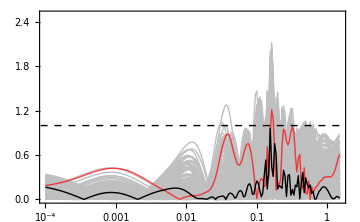

```mathematica
Module[{curves,styles,legendLabels},curves=Join[Table[AccGAλσ[i],{i,Select[Range[Length[Params]],#!=BestFit&&#!=WorstFit&]}],{AccGAλσ[WorstFit],AccGAλσ[BestFit]}];
styles=Join[Table[Directive[Thin,GrayLevel[0.75]],{Length[Params]-2}],{Directive[Thick,Red,Opacity[0.7]](*Worst fit*),
Directive[Thick,Black](*Best fit*)}];
legendLabels={(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Test set}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Worst fit}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Best fit}"]};
ListLogLinearPlot[curves,Joined->True,PlotRange->{{10^-4,1.5},{0,2.5}},PlotStyle->styles,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"k~[h / \\text{Mpc}]","\\text{Acc}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLegends->Placed[LineLegend[styles[[-3;;]],legendLabels,LegendLayout->{"Row",3},LabelStyle->{Black,Bold,14},LegendFunction->"Frame",LegendMarkerSize->{35,15}],{0.212,0.7}],Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]}},ImageSize->Medium]//Quiet]//Quiet
```

### Correction: Full Emulator

```mathematica
(* Formula for (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
DDPkclass[h_,ωb_,ωm_,ns_,As_]:=-10^((ωb+10.904067-Cos[h]-(1.1083639/(h+3 ωb)+Log[ns]+6.28427 ωm+ωm))+0.43375605 Log[As]) 
λFixed=0.4;
(* Compute (d^2 Subscript[P, GA])/dk^2 at Subscript[k, eq] and solve for σ by equaling to (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
(* Fix λ = 0.4 *)
DDP=Table[D[D[PGA[k,Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]*Pc[k,Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],σ,λFixed],k],k]/.k->keq[Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]]],{i,1,Length[Params]}]//Simplify;
σDDP=Table[Solve[DDP[[i]]==DDPkclass[Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]]],σ]//Quiet,{i,Length[Params]}];
(* Take the smallest one in absolute value *)
MinAbsKeepSign[pair_]:=First@MinimalBy[pair,Abs]
σFullGA=MinAbsKeepSign/@Table[{Re[σDDP[[i]][[1,1,2]]],Re[σDDP[[i]][[2,1,2]]]},{i,1,Length[Params]}];
```

```mathematica
AccGAσFullGA[i_]:=Table[{PkData[[i]][[j,1]],Abs[1-(PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]*Pc[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],σFullGA[[i]],λFixed])/PkData[[i]][[j,2]]]*100},{j,1,Length[PkData[[i]]]}]
```

```mathematica
{Mean[#],Min[#],Max[#],Position[#,Min[#]],Position[#,Max[#]]}&@Table[Mean[AccGAσFullGA[i][[All,2]]],{i,1,Length[Params]}]//Quiet
WorstFit=Position[#,Max[#]][[1,1]]&@Table[Mean[AccGAσFullGA[i][[All,2]]],{i,1,Length[Params]}]//Quiet;
BestFit=Position[#,Min[#]][[1,1]]&@Table[Mean[AccGAσFullGA[i][[All,2]]],{i,1,Length[Params]}]//Quiet;
```

{0.307261,0.143554,0.623129,{{69}},{{83}}}

```mathematica
AccGAσ[i_][σ_]:=Table[{PkData[[i]][[j,1]],Abs[1-(PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]*Pc[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],σ,λFixed])/PkData[[i]][[j,2]]]*100},{j,1,Length[PkData[[i]]]}]
```

```mathematica
i=4;
Print["Blue: Original"]
Print["Black: ",(MaTeX["\\sigma",Magnification->1.2])," = ",σDDP[[i]][[1,1,2]]]
Print["Red: ",(MaTeX["\\sigma",Magnification->1.2])," = ",σDDP[[i]][[2,1,2]]]
ListLogLinearPlot[{AccGA[i],AccGAσ[i][Re[σDDP[[i]][[1,1,2]]]],AccGAσ[i][σDDP[[i]][[2,1,2]]]},Joined->True,PlotRange->{All,{Automatic,3.6}},PlotStyle->{Directive[Blue],Directive[Black],Directive[Red]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\text{Acc}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->18},Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]}},ImageSize->480]//Quiet
i=.;
```

```mathematica
Module[{curves,styles,legendLabels},curves=Join[Table[AccGAσFullGA[i],{i,Select[Range[Length[Params]],#!=BestFit&&#!=WorstFit&]}],{AccGAσFullGA[WorstFit],AccGAσFullGA[BestFit]}];
styles=Join[Table[Directive[Thin,GrayLevel[0.75]],{Length[Params]-2}],{Directive[Thick,Red,Opacity[0.7]](*Worst fit*),
Directive[Thick,Black](*Best fit*)}];
legendLabels={(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Test set}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Worst fit}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Best fit}"]};
ListLogLinearPlot[curves,Joined->True,PlotRange->{{10^-4,1.5},All},PlotStyle->styles,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"k~[h / \\text{Mpc}]","\\text{Acc}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLegends->Placed[LineLegend[styles[[-3;;]],legendLabels,LegendLayout->{"Row",3},LabelStyle->{Black,Bold,14},LegendFunction->"Frame",LegendMarkerSize->{35,15}],{0.212,0.7}],Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]}},ImageSize->Medium]//Quiet]//Quiet
```

```mathematica
Comparisonσ=Table[{AccGAσFullGA[i][[All,2]]//Mean,AccGA[i][[All,2]]//Mean},{i,Length[Params]}];
Posσ=Position[Comparisonσ,{a_,b_}/;b<a]//Flatten
Length[Posσ]
```

{2,7,12,15,18,19,21,23,59,60,61,75,82,83,95,109,110,118,120,126,128,131,133,137,139,140,144,149,158,163,177,179,186,188,196}

35

```mathematica
ValidIndices=Complement[Range[Length[PkData]],Posσ];AccGAσLast=Table[Table[{PkData[[i]][[j,1]],Abs[1-(PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]*Pc[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],σFullGA[[i]],λFixed])/PkData[[i]][[j,2]]]*100},{j,1,Length[PkData[[i]]]}],{i,ValidIndices}];
```

```mathematica
{Mean[#],Min[#],Max[#],Position[#,Min[#]],Position[#,Max[#]]}&@Table[Mean[AccGAσLast[[i]][[All,2]]],{i,1,Length[ValidIndices]}]//Quiet
WorstFit=Position[#,Max[#]][[1,1]]&@Table[Mean[AccGAσLast[[i]][[All,2]]],{i,1,Length[ValidIndices]}]//Quiet;
BestFit=Position[#,Min[#]][[1,1]]&@Table[Mean[AccGAσLast[[i]][[All,2]]],{i,1,Length[ValidIndices]}]//Quiet;
```

{0.29401,0.143554,0.498984,{{58}},{{123}}}

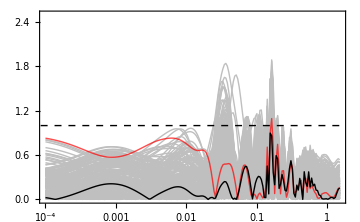

```mathematica
Module[{curves,styles,legendLabels},curves=Join[Table[AccGAσLast[[i]],{i,Select[Range[Length[ValidIndices]],#!=BestFit&&#!=WorstFit&]}],{AccGAσLast[[WorstFit]],AccGAσLast[[BestFit]]}];
styles=Join[Table[Directive[Thin,GrayLevel[0.75]],{Length[ValidIndices]-2}],{Directive[Thick,Red,Opacity[0.7]](*Worst fit*),
Directive[Thick,Black](*Best fit*)}];
legendLabels={(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Test set}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Worst fit}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Best fit}"]};
ListLogLinearPlot[curves,Joined->True,PlotRange->{{10^-4,1.5},{0,2.5}},PlotStyle->styles,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"k~[h / \\text{Mpc}]","\\text{Acc}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLegends->Placed[LineLegend[styles[[-3;;]],legendLabels,LegendLayout->{"Row",3},LabelStyle->{Black,Bold,14},LegendFunction->"Frame",LegendMarkerSize->{35,15}],{0.212,0.7}],Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]}},ImageSize->Medium]//Quiet]//Quiet
```